## With back dispersal

```mathematica
Clear["Global`*"];
```

```mathematica
cm=72/2.54;
```

```mathematica
style=Directive[FontFamily->"Arial",FontSize->12];
blue=RGBColor["#0A71B7"]
orange= RGBColor["#D25F02"]
```

RGBColor[0.0392156862745098, 0.44313725490196076, 0.7176470588235294]

RGBColor[0.8235294117647058, 0.37254901960784315, 0.00784313725490196]

```mathematica
QR[n_]:= 1/n(1/2+1/2 Q0)+(n-1)/n Q1 ;
```

```mathematica
(1/4+1/4(1-backmp (1-α))^2+1/2 (1-backmp (1-α)))  //Simplify
% == (1/2+1/2(1-backmp (1-α)))^2//Simplify
```

1/4 (2+backmp (-1+α))^2

True

```mathematica
(1/4 QR[n]+1/4(1-mp (1-α))^2 QR[n]+1/2 (1-mp (1-α))QR[n])/.mp->0 //Simplify
```

(1+Q0+2 (-1+n) Q1)/(2 n)

```mathematica
solFstPairs3=Solve[{ 
Q0 ==(1-e)( α  (1/2+1/2 Q0) + (1-α) (1-mp)QR[n])+ e (α  (1/2+1/2 Q0) + (1-α) 1/k(1/2+1/2 Q0)),

Q1 ==(1-e)(1-m)^2(1/4 QR[n]+1/4(1-mp (1-α))^2 QR[n]+1/2 (1-mp (1-α))QR[n])+ e/k  (1/2+1/2 Q0)

},{Q0,Q1}] //Simplify //Flatten  ;
```

```mathematica
FST == Q1;
FIS ==(Q0-Q1)/(1-Q1);
FIT == Q0 ;
(* See Rousset p. 18 *)
```

```mathematica
(Q0-Q1)/(1-Q1) /. solFstPairs3 /.α->0 /.mp->0 //Simplify 
Limit[%,n-> ∞]//Simplify 
%/.k->1 //Simplify
(Q0-Q1)/(1-Q1) /. solFstPairs3 /.α->0 /.mp->0 /.k->n //Simplify ;
Limit[%,n-> ∞]//Simplify
```

-((-1+e) (-2+m) m (k+e (-1+n)))/(e^2 (-2+m) m (-1+n)+k (-2+m) m (-1+2 n)+e (-2 (-1+k) n+m^2 (1+k-n-2 k n)+2 m (-1-k+n+2 k n)))

-((-1+e) e (-2+m) m)/(e^2 (-2+m) m+2 k (-2+m) m-e (-2+2 k (-1+m)^2-2 m+m^2))

e/(2-e)

0

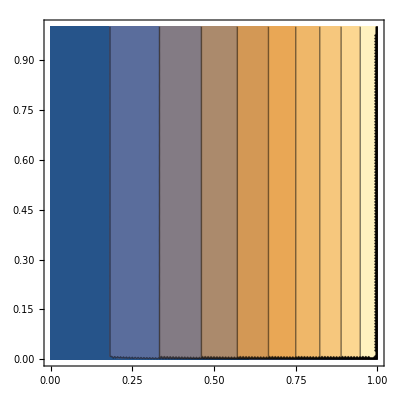

```mathematica
ContourPlot[-((-1+e) e (-2+m) m)/(e^2 (-2+m) m+2 k (-2+m) m-e (-2+2 k (-1+m)^2-2 m+m^2))/.k->1,{e,0,1},{m,0,1}]
```

```mathematica
Q0/. solFstPairs3 /.α->0 /.mp->0 //Simplify 
Limit[%,n-> ∞]//Simplify 
%/.k->1 //Simplify
Q0/. solFstPairs3 /.α->0 /.mp->0 /.k->n //Simplify ;
Limit[%,n-> ∞]//Simplify
```

((-1+e) k-e ((-1+e) m^2 (-1+n)+n+2 m (-1+e+n-e n)))/(k (-1+e (1+4 m (-1+n)-2 m^2 (-1+n)-2 n)-4 m (-1+n)+2 m^2 (-1+n))+e ((-1+e) m^2 (-1+n)+n+2 m (-1+e+n-e n)))

(e (-1+2 (-1+e) m-(-1+e) m^2))/(e^2 (-2+m) m+2 k (-2+m) m-e (-1+2 k (-1+m)^2-2 m+m^2))

-(e (1-2 (-1+e) m+(-1+e) m^2))/(2 (-2+m) m+e^2 (-2+m) m+e (-1+6 m-3 m^2))

0

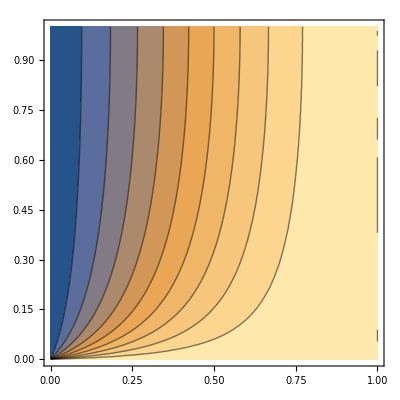

```mathematica
ContourPlot[-(e (1-2 (-1+e) m+(-1+e) m^2))/(2 (-2+m) m+e^2 (-2+m) m+e (-1+6 m-3 m^2)),{e,0,1},{m,0,1}]
```

```mathematica
zbar = (zi + zj+(n-2)z0)/n;
localseeds = f n zbar (* also equal to ovules *);
paraseeds = f n z ;
```

```mathematica
(* fitness through male function *)
wmale = (1-e)n ( (α zi f+(1-α)localseeds (1-mp) (1-zi)/(n  (1-zbar)) )( (1-m)/localseeds +((1-e)m)/((1-e)paraseeds)+e/((1-e)paraseeds) )+  (1-e)(1-α)paraseeds  mp (1-zi)/(n  (1-e) (1-z))( (1-m)/paraseeds +((1-e)m)/((1-e)paraseeds)+e/((1-e)paraseeds) ) ) ;
(* fitness through female function *)
wfemale = (1-e)n f zi ( (1-m)/localseeds + m (1-e)1/((1-e)paraseeds) +  e 1/((1-e)paraseeds)) ;

monopop = {zi-> z,zj-> z,z0->z}
```

{zi→z,zj→z,z0→z}

```mathematica
wmale/.monopop //Simplify
wfemale/.monopop //Simplify
```

1

1

```mathematica
w =1/2( wmale+ wfemale );
```

```mathematica
D[w,zi]+ (n-1)D[w,zj]+D[w,z]/.monopop  //Simplify
```

0

```mathematica
D[w,zi] /.r-> (2Q1)/(1+Q0) /.monopop  /. solFstPairs3 ;
soln3Direct=Flatten@Solve[%==0,z] //Simplify
```

{z→(e (-1+m) (2+mp (-1+α))-(-1+n) (1+α)+m (-2+mp-mp α))/(2-mp-2 n+e (-1+m) (2+mp (-1+α))+mp α+m (-2+mp-mp α))}

```mathematica
D[w,zj] /.r-> (2Q1)/(1+Q0) /.monopop  /. solFstPairs3 ;
soln3Indirect=Flatten@Solve[%==0,z] //Simplify
```

{z→(1+e (-1+m) (2+mp (-1+α))+α+m (-2+mp-mp α))/((-1+e) (-1+m) (2+mp (-1+α)))}

```mathematica
D[w,zi]+ (n-1)r D[w,zj]/.r-> (2Q1)/(1+Q0) /.monopop  /. solFstPairs3 ;
soln3=Flatten@Solve[%==0,z] //Simplify

% /. α ->a
```

{z→(4 e^2 (-1+m) (-1+n) (2+mp (-1+α))+e (-4 (-1+n) (-1+m (2+mp (-1+α))-α)-k (-1+m) (2+mp (-1+α)) (m (-1+n) (2+mp (-1+α)) (1+α)-2 (1+n-α+n α)-mp (-1+n) (-1+α^2)))+k (m^2 (-1+n) (2+mp (-1+α))^2 (1+α)+mp (-1+n) (4+mp (-1+α)) (-1+α^2)-2 m (2+mp (-1+α)) (2 (n-α+n α)+mp (-1+n) (-1+α^2))))/(4 e^2 (-1+m) (-1+n) (2+mp (-1+α))+2 k (mp+m (2+mp (-1+α))-mp α) (2-4 n+m (-1+n) (2+mp (-1+α))+mp (-1+n+α-n α))-2 e (-1+m) (2+mp (-1+α)) (2 (-1+n)+k (-2 n+m (-1+n) (2+mp (-1+α))+mp (-1+n+α-n α))))}

{z→(4 e^2 (-1+m) (2+(-1+a) mp) (-1+n)+k ((1+a) m^2 (2+(-1+a) mp)^2 (-1+n)+(-1+a^2) mp (4+(-1+a) mp) (-1+n)-2 m (2+(-1+a) mp) ((-1+a^2) mp (-1+n)+2 (-a+n+a n)))+e (-4 (-1-a+m (2+(-1+a) mp)) (-1+n)-k (-1+m) (2+(-1+a) mp) (-((-1+a^2) mp (-1+n))+(1+a) m (2+(-1+a) mp) (-1+n)-2 (1-a+n+a n))))/(4 e^2 (-1+m) (2+(-1+a) mp) (-1+n)+2 k (mp-a mp+m (2+(-1+a) mp)) (2+m (2+(-1+a) mp) (-1+n)-4 n+mp (-1+a+n-a n))-2 e (-1+m) (2+(-1+a) mp) (2 (-1+n)+k (m (2+(-1+a) mp) (-1+n)-2 n+mp (-1+a+n-a n))))}

```mathematica
z/.soln3 /. e->0  /.mp->0//FullSimplify;
% ==1/2( 1+α+(1-α)/(n+(n-1)(1-m)) )//Simplify
```

True

```mathematica
z/.soln3 /. e->0  /.mp->0 /. m-> 1 /. α-> 0 //Together //FullSimplify
```

(1+n)/(2 n)

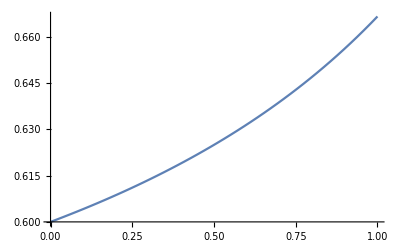

```mathematica
Plot[1/2+1/2 1/(n+(n-1)(1-m))/.n->3,{m,0,1}]
```

```mathematica
z/.soln3  /.mp->0 /. m-> δ m /.n-> n/δ ;
Series[%,{δ,0,0}]
```

(-1+2 e+k-α+k α)/(2 (-1+e+k))+O[δ]^1

```mathematica
Apart[(-1+2 e+k-α+k α)/(2 (-1+e+k)) ,k]
```

(1+α)/2+(e-e α)/(2 (-1+e+k))

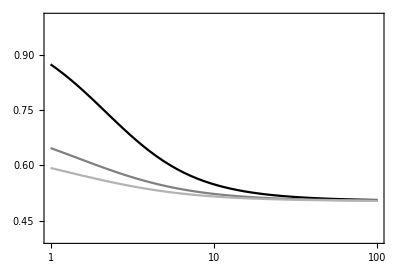

```mathematica
LogLinearPlot[Evaluate[z /. soln3 /. n-> 100/. m-> 0.1/.k->{1,2,3} /.mp->0.0 /.α-> 0. /. e->1/(1+Nt)],{Nt,1,100},PlotRange->{0.4,1},AxesOrigin->{1,0.5},Frame-> True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],PlotStyle->{GrayLevel[0],GrayLevel[0.5],GrayLevel[0.7]},ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5] 
(* Export["/Users/admin/Dropbox/Projects/SexAllocation/PlotZExt1BackD.pdf",%,Background->None]; *)
```

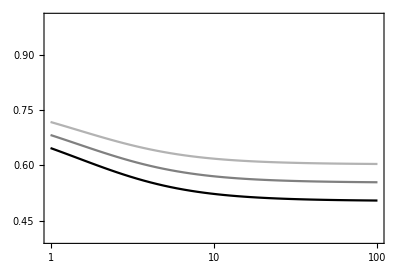

```mathematica
LogLinearPlot[Evaluate[z /. soln3 /. n-> 100/. m-> 0.1/.k->2 /.mp->0.0 /.α-> {0.,0.1,0.2} /. e->1/(1+Nt)],{Nt,1,100},PlotRange->{0.4,1},AxesOrigin->{1,0.5},Frame-> True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],PlotStyle->{GrayLevel[0],GrayLevel[0.5],GrayLevel[0.7]},ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5]
(*Export["/Users/admin/Dropbox/Projects/SexAllocation/PlotZExt2BackD.pdf",%,Background->None];*)
```

```mathematica
z/.soln3  /.mp->δ mp /. m-> δ m /.n-> n/δ /.α-> α δ /.e-> e δ;
Series[%,{δ,0,1}] //Simplify ;
Normal@% /. δ->1 ;
% == 1/2(1+α+((2 e+2 m-mp) (n e +k))/(2 n (e (k-1)+k (2 m+mp)))) //Simplify
```

True

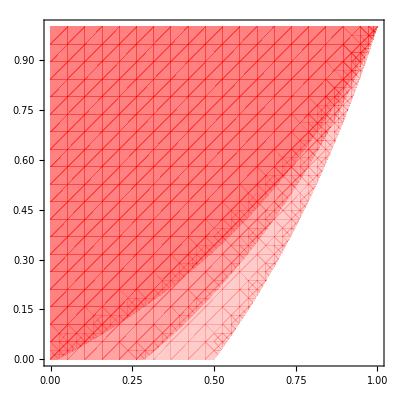

CreateDirectory::privv: Privilege violation for file or directory /Users/admin/Dropbox/.

Export::nodir: Directory /Users/admin/Dropbox/Projects/SexAllocation/ does not exist.

Export::noopen: Cannot open /Users/admin/Dropbox/Projects/SexAllocation/PlotContour1BackD.pdf.

```mathematica
RegionPlot[Evaluate[Table[z>1/2/. soln3 /. n-> 100 /.k->1 /. e->1/(1+Nt)/. α->0.,{Nt,{2,5,100}}]],{mp,0,1},{m,0,1},LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,PlotStyle->Directive[Red,Opacity[0.2]],BoundaryStyle->None]
Export["/Users/admin/Dropbox/Projects/SexAllocation/PlotContour1BackD.pdf",%,Background->None];
```

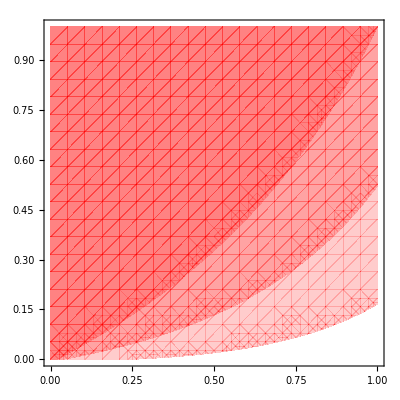

CreateDirectory::privv: Privilege violation for file or directory /Users/admin/Dropbox/.

Export::nodir: Directory /Users/admin/Dropbox/Projects/SexAllocation/ does not exist.

Export::noopen: Cannot open /Users/admin/Dropbox/Projects/SexAllocation/PlotContour2BackD.pdf.

```mathematica
RegionPlot[Evaluate[Table[z>1/2/. soln3 /. n-> 100 /.k->1 /. e->1/(1+100),{α,{0.,0.005,0.01}}]],{mp,0,1},{m,0,1},LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,PlotStyle->Directive[Red,Opacity[0.2]],BoundaryStyle->None]
Export["/Users/admin/Dropbox/Projects/SexAllocation/PlotContour2BackD.pdf",%,Background->None];
```

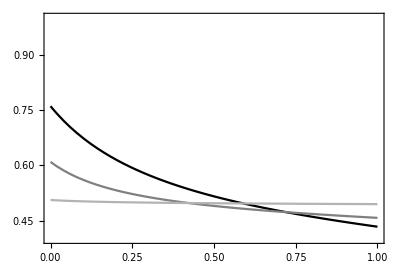

CreateDirectory::privv: Privilege violation for file or directory /Users/admin/Dropbox/.

Export::nodir: Directory /Users/admin/Dropbox/Projects/SexAllocation/ does not exist.

Export::noopen: Cannot open /Users/admin/Dropbox/Projects/SexAllocation/PlotZEquiSeedBackDisp1.pdf.

```mathematica
Plot[Evaluate[z /. soln3 /. n-> 100 /.k->1 /. e->1/(1+Nt)/. Nt-> {2,5,100}/. α->0 /. m-> 0.1],{mp,0,1},PlotRange->{0.4,1},AxesOrigin->{1,0.5},Frame-> True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],PlotStyle->{GrayLevel[0],GrayLevel[0.5],GrayLevel[0.7]},ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5]
Export["/Users/admin/Dropbox/Projects/SexAllocation/PlotZEquiSeedBackDisp1.pdf",%,Background->None];
```

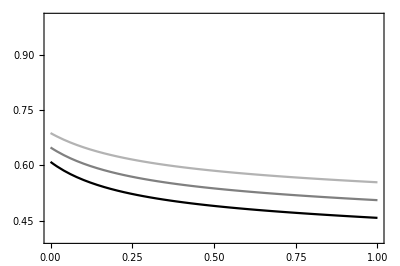

CreateDirectory::privv: Privilege violation for file or directory /Users/admin/Dropbox/.

Export::nodir: Directory /Users/admin/Dropbox/Projects/SexAllocation/ does not exist.

Export::noopen: Cannot open /Users/admin/Dropbox/Projects/SexAllocation/PlotZEquiSeedBackDisp2.pdf.

```mathematica
Plot[Evaluate[z /. soln3 /. n-> 100 /.k->1 /. e->1/(1+Nt)/. Nt->5/. α->{0,0.1,0.2} /. m-> 0.1],{mp,0,1},PlotRange->{0.4,1},AxesOrigin->{1,0.5},Frame-> True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],PlotStyle->{GrayLevel[0],GrayLevel[0.5],GrayLevel[0.7]},ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5]
Export["/Users/admin/Dropbox/Projects/SexAllocation/PlotZEquiSeedBackDisp2.pdf",%,Background->None];
```

```mathematica
sims=Table[
(*FIS,FIT,FST*){(Q0-Q1)/(1-Q1),Q0,Q1,z}/. solFstPairs3 /. soln3/.k->1/. n-> 100 /. m->  RandomChoice[{0.001,0.005,0.01,0.05,0.1,0.5,1,5,10.,50,100}]/100 /. e->RandomChoice[{0,0.05,0.1,0.15,0.2,0.25,.3}] /.mp ->0. /. α->0.
,{i,100}];
```

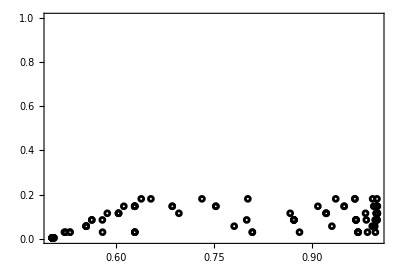

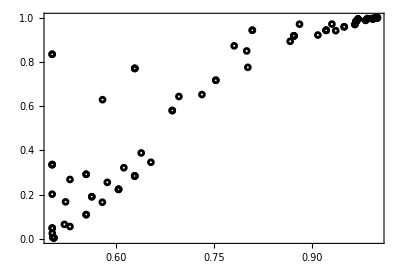

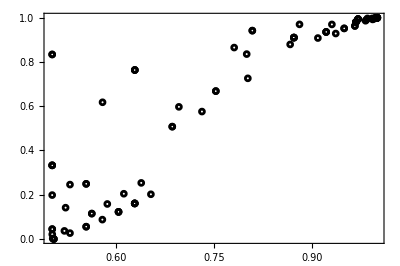

```mathematica
ListPlot[ sims[[All,{4,1}]] ,Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Black,Thickness[0.1],Circle[]},ImageSize->5],PlotRange->{{.5,1},{0,1}}] 
ListPlot[ sims[[All,{4,2}]] ,Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Black,Thickness[0.1],Circle[]},ImageSize->5],PlotRange->{{.5,1},{0,1}}] 
ListPlot[ sims[[All,{4,3}]] ,Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Black,Thickness[0.1],Circle[]},ImageSize->5],PlotRange->{{.5,1},{0,1}}]
```

```mathematica
sims=Table[
{(Q0-Q1)/(1-Q1),Q0,Q1,z}/. solFstPairs3 /. soln3/.k->  RandomChoice[{1,2,3,4,5,6}]/. n-> 1000 /. m->  RandomReal[{0,0.1}]   /. e->RandomReal[{0.005,.5}]   /.mp ->RandomReal[{0,.1}]  /. α-> RandomReal[{0.,1.}]
,{i,100}];
(*Export["/Users/admin/Dropbox/Projects/SexAllocation/Sims_BackwardDisp.csv",sims]*)
```

```mathematica
simsCamille=Table[
{(Q0-Q1)/(1-Q1),Q0,Q1,z}/. solFstPairs3 /. soln3//.k->  RandomChoice[{1,2,3,4,5,6}]/. n-> 1000 /. m->  RandomReal[{0,0.1}]   /. e->RandomReal[{0.005,.5}]   /.mp ->RandomReal[{0,.1}]  /. α-> RandomReal[{0.,1.}] 
,{i,500}];
 Export["/Users/cmullon/Dropbox/Projects/SexAllocation/Sims_BackwardDisp_Camille.csv",simsCamille]
```

/Users/cmullon/Dropbox/Projects/SexAllocation/Sims_BackwardDisp_Camille.csv

```mathematica
simsImport=Import["/Users/cmullon/Dropbox/Projects/SexAllocation/Sims_BackwardDisp_Camille.csv"];
```

```mathematica
samples = 500;
```

```mathematica
data=simsImport[[All,{4,1}]] ;
dataPlot=RandomSample[simsImport[[All,{4,1}]],samples] ;
p11=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p12=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p1 = Show[p11,p12] ;

data=simsImport[[All,{4,2}]] ;
dataPlot=RandomSample[simsImport[[All,{4,2}]],samples] ;
p21=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p22=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p2 = Show[p21,p22] ;

data=simsImport[[All,{4,3}]] ;
dataPlot=RandomSample[simsImport[[All,{4,3}]],samples] ;
p31=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p32=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p3 = Show[p31,p32] ;
```

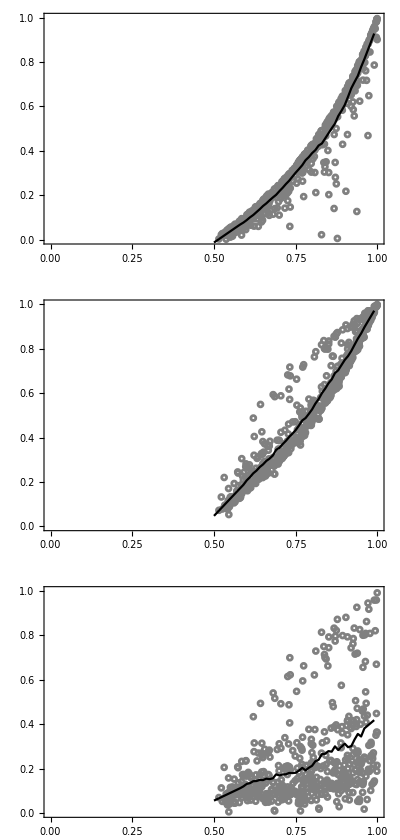

/Users/cmullon/Dropbox/Projects/SexAllocation/AssoF_backD_Camille.pdf

```mathematica
GraphicsColumn[{p1,p2,p3}] 
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/AssoF_backD_Camille.pdf",%]
```

```mathematica
simsCamille=Table[
{(Q0-Q1)/(1-Q1),Q0,Q1,z}/. solFstPairs3 /. soln3/.k->  RandomChoice[{1,2,3,4,5,6}]/. n-> 1000 /. m->  RandomReal[{0,0.1}]   /. e->RandomReal[{0.005,.5}]   /.mp ->RandomReal[{0,.1}]  /. α-> 0. 
,{i,500}];
 Export["/Users/cmullon/Dropbox/Projects/SexAllocation/SimsRandomMating_BackwardDisp_Camille.csv",simsCamille]
```

/Users/cmullon/Dropbox/Projects/SexAllocation/SimsRandomMating_BackwardDisp_Camille.csv

```mathematica
simsImport=Import["/Users/cmullon/Dropbox/Projects/SexAllocation/SimsRandomMating_BackwardDisp_Camille.csv"];
```

```mathematica
data=simsImport[[All,{4,1}]] ;
dataPlot=RandomSample[simsImport[[All,{4,1}]],samples] ;
p11=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p12=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p1 = Show[p11,p12] ;

data=simsImport[[All,{4,2}]] ;
dataPlot=RandomSample[simsImport[[All,{4,2}]],samples] ;
p21=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p22=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p2 = Show[p21,p22] ;

data=simsImport[[All,{4,3}]] ;
dataPlot=RandomSample[simsImport[[All,{4,3}]],samples] ;
p31=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p32=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p3 = Show[p31,p32] ;
```

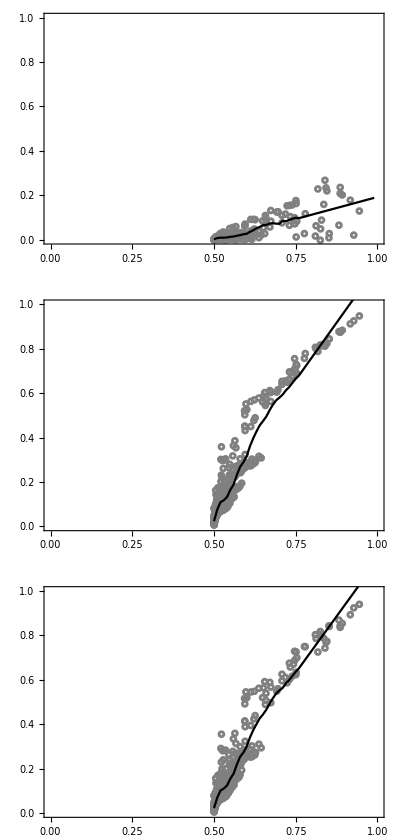

```mathematica
GraphicsColumn[{p1,p2,p3}]
```

```mathematica
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/AssoFRandomMating_BackwardDisp_Camille.pdf",%]
```

/Users/cmullon/Dropbox/Projects/SexAllocation/AssoFRandomMating_BackwardDisp_Camille.pdf

```mathematica
simsCamille=Table[
{(Q0-Q1)/(1-Q1),Q0,Q1,z}/. solFstPairs3 /. soln3/.k->  RandomChoice[{1,2,3,4,5,6}]/. n-> 1000 /. m->  RandomReal[{0,0.1}]   /. e->RandomReal[{0.005,.5}]   /.mp ->0. /. α->0.
,{i,500}];
```

```mathematica
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/SimsRandomMating_NoPolDisp_BackwardDisp_Camille.csv",simsCamille]
```

/Users/cmullon/Dropbox/Projects/SexAllocation/SimsRandomMating_NoPolDisp_BackwardDisp_Camille.csv

```mathematica
simsImport=Import["/Users/cmullon/Dropbox/Projects/SexAllocation/SimsRandomMating_NoPolDisp_BackwardDisp_Camille.csv"];
```

```mathematica
data=simsImport[[All,{4,1}]] ;
dataPlot=RandomSample[simsImport[[All,{4,1}]],samples] ;
p11=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p12=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p1 = Show[p11,p12] ;

data=simsImport[[All,{4,2}]] ;
dataPlot=RandomSample[simsImport[[All,{4,2}]],samples] ;
p21=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p22=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p2 = Show[p21,p22] ;

data=simsImport[[All,{4,3}]] ;
dataPlot=RandomSample[simsImport[[All,{4,3}]],samples] ;
p31=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p32=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p3 = Show[p31,p32] ;
```

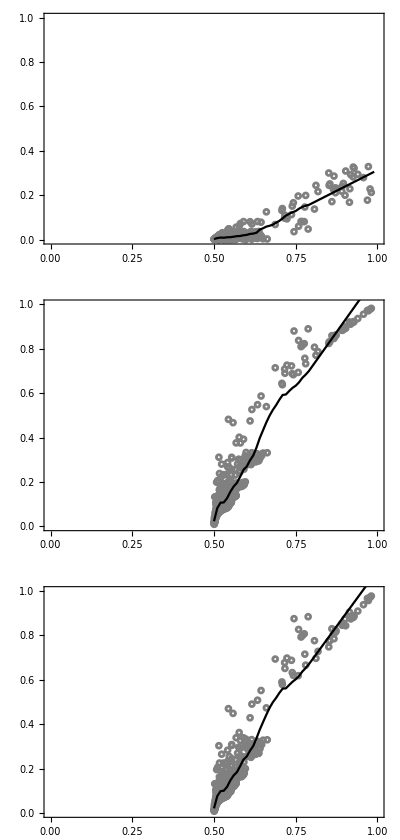

```mathematica
GraphicsColumn[{p1,p2,p3}]
```

```mathematica
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/SimsRandomMating_NoPolDisp_BackwardDisp_Camille.pdf",%]
```

/Users/cmullon/Dropbox/Projects/SexAllocation/SimsRandomMating_NoPolDisp_BackwardDisp_Camille.pdf

```mathematica
test={(Q0-Q1)/(1-Q1),Q0,Q1,z}/. solFstPairs3 /. soln3/.k->1/. n-> 100 /.mp ->0/. α-> 0  //Simplify
```

{(1+99 e)/(199-99 e),(-1-99 e^2 (-2+m) m+99 e (-1-2 m+m^2))/(-1-396 m+99 e^2 (-2+m) m+198 m^2-99 e (1-6 m+3 m^2)),(-(-1+m)^2+e (-99-2 m+m^2))/(-1-396 m+99 e^2 (-2+m) m+198 m^2-99 e (1-6 m+3 m^2)),(198 e^2 (-1+m)+m (-200+99 m)+e (-2+2 m-99 m^2))/(2 (99 e^2 (-1+m)+m (-199+99 m)+e (-1+100 m-99 m^2)))}

```mathematica
test /. e-> 0.8 /. m-> 0.01
```

{0.669449,0.998046,0.99409,0.996956}

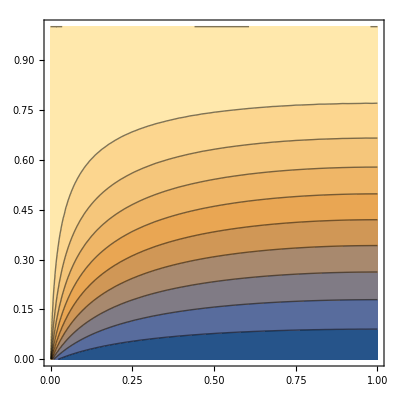

```mathematica
ContourPlot[test[[2]],{m,0,1},{e,0,1}]
```

```mathematica
sims=Table[
{(Q0-Q1)/(1-Q1),Q0,Q1,z}/. solFstPairs3 /. soln3/.k->10/. n-> 100 /. m->  RandomChoice[{0.001,0.005,0.01,0.05,0.1,0.5,1,5,10.,50,100}]/100 /. e->RandomChoice[{0,0.05,0.1,0.15,0.2,0.25,.3}] /.mp ->0. /. α->0.9
,{i,1000}];
```

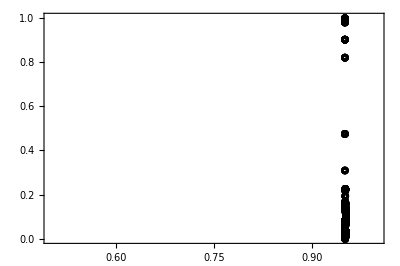

```mathematica
ListPlot[ sims[[All,{4,3}]] ,Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Black,Thickness[0.1],Circle[]},ImageSize->5],PlotRange->{{.5,1},{0,1}}]
```

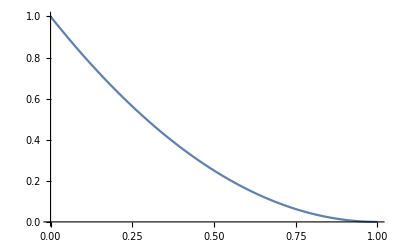

```mathematica
Plot[(1-m)^2,{m,0,1}]
```

```mathematica
data=Import["/Users/cmullon/Dropbox/Projects/SexAllocation/DB_test_Means_Svariance.csv","Data"];
```

Import::nffil: File not found during Import.

```mathematica
data=Partition[Flatten[data],3];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

```mathematica
ngen = Length[data] ;
```

```mathematica
{Q1,Q0,(Q0-Q1)/(1-Q1)} /.solFstPairs3 /.α->0/. m-> IC/n/.IC-> 100/. n-> 100 /.k->1 /.e->0.3/.mp->0 //N
Map[Mean,Flatten[data,{2}]]
```

{0.202007,0.346711,0.181335}

Flatten::fldep: Level 2 specified in {{2}} exceeds the levels, 1, which can be flattened together in Flatten[].

Mean[Flatten[]]

```mathematica
ListPlot[Flatten[data,{2}]]
```

Flatten::fldep: Level 2 specified in {{2}} exceeds the levels, 1, which can be flattened together in Flatten[].

Flatten::flpi: Levels to be flattened together in {2.} should be lists of positive integers.

Flatten::fldep: Level 2 specified in {{2}} exceeds the levels, 1, which can be flattened together in Flatten[].

ListPlot::lpn: Flatten[Flatten[],{2.}] is not a list of numbers or pairs of numbers.

ListPlot[Flatten[Flatten[],{2}]]

```mathematica
Map[Mean,Flatten[data[[5;;ngen]],{2}]]
```

Part::take: Cannot take positions 5 through 0 in Flatten[].

Flatten::fldep: Level 2 specified in {{2}} exceeds the levels, 1, which can be flattened together in Flatten[]⟦5;;0⟧.

Mean[Flatten[]⟦5;;0⟧]

```mathematica
data=Import["/Users/cmullon/Dropbox/Projects/SexAllocation/DB_test_Means_Svariance2.csv","Data"];
```

Import::nffil: File not found during Import.

```mathematica
data=Partition[Flatten[data],6];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

```mathematica
ngen = Length[data] ;
```

```mathematica
{Q1,Q0,Q0,(1/(2n)+1/(2n)Q0+(1-1/n)Q1)  ,(Q0-Q1)/(1-Q1),(Q0-Q1)/(1-Q1) } /.solFstPairs3 /.α->0/. m-> 0.3/. n-> 3 /.k->1 /.e->0.1/.mp->0 //N
Map[Mean,Flatten[data,{2}]]//Expand
```

{0.251681,0.438761,0.438761,0.407581,0.25,0.25}

Flatten::fldep: Level 2 specified in {{2}} exceeds the levels, 1, which can be flattened together in Flatten[].

Mean[Flatten[]]

```mathematica
ListPlot[Flatten[data,{2}]]
```

Flatten::fldep: Level 2 specified in {{2}} exceeds the levels, 1, which can be flattened together in Flatten[].

ListPlot::lpn: Flatten[Flatten[],{2.}] is not a list of numbers or pairs of numbers.

ListPlot[Flatten[Flatten[],{2}]]

```mathematica
Sum[p[i,j] p[i,k] ,{j,1,3},{k,1,3}] == Sum[p[i,j]^2 ,{j,1,3} ]+ (  Sum[p[i,j] p[i,k] ,{j,1,3},{k,1,3}] - Sum[p[i,j]^2 ,{j,1,3} ])
```

True

```mathematica
pij + (n-1)/n pijpik - 1/n(pij - pij1pij2) /. pijpik -> Fst pij + (1-Fst) pij^2 /. pij1pij2 -> FIt pij + (1-FIt) pij^2   //Simplify
```

(pij (-1+FIt+n-FIt pij+n pij+Fst (-1+n+pij-n pij)))/n

```mathematica
data=Import["/Users/cmullon/Dropbox/Projects/SexAllocation/DB_test_Means_Svariance_diallelic.csv","Data"];
```

Import::nffil: File not found during Import.

```mathematica
data=Partition[Flatten[data],6];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

```mathematica
ngen = Length[data] ;
```

```mathematica
1/(2n-1) /.n->10 //N
```

0.0526316

```mathematica
{Q1,Q0,Q0,(1/(2n)+1/(2n)Q0+(1-1/n)Q1),(Q0-Q1)/(1-Q1)  } /.solFstPairs3 /.α->0/. m-> 0.05/. n-> 2 /.k->1 /.e->0.1/.mp->0 //N
Map[Mean,Flatten[data,{2}]] //N
```

{0.799108,0.875308,0.875308,0.868381,0.37931}

Flatten::fldep: Level 2 specified in {{2}} exceeds the levels, 1, which can be flattened together in Flatten[].

Mean[Flatten[]]

```mathematica
ListLinePlot[Flatten[data,{2}]]
```

Flatten::fldep: Level 2 specified in {{2}} exceeds the levels, 1, which can be flattened together in Flatten[].

ListLinePlot::lpn: Flatten[Flatten[],{2.}] is not a list of numbers or pairs of numbers.

ListLinePlot[Flatten[Flatten[],{2}]]

```mathematica
Map[Mean,Flatten[data[[30;;ngen]],{2}]]
```

Part::take: Cannot take positions 30 through 0 in Flatten[].

Flatten::fldep: Level 2 specified in {{2}} exceeds the levels, 1, which can be flattened together in Flatten[]⟦30;;0⟧.

Mean[Flatten[]⟦30;;0⟧]

```mathematica
FST == Q1;
FIS ==(Q0-Q1)/(1-Q1);
FIT == Q0 ;
```

```mathematica
Solve[FST == (FIT - FIS)/(1-FIS) ,FIS]
```

{{FIS→(-FIT+FST)/(-1+FST)}}

### haploids

```mathematica
Clear["Global`*"];
```

```mathematica
(* Eq. 8 of Rousset Effective size in simple metapopulation models 2003 Heredity *)
solFstHap=Solve[

Q1 ==(1-e)(1-m)^2(1/n+ (1-1/n)Q1)+ e 1/k 

,Q1] //Simplify //Flatten  ;
```

```mathematica
solFstHap
```

{Q1→(-(-1+e) k (-1+m)^2+e n)/(k (1+e (-1+m)^2 (-1+n)+2 m (-1+n)-m^2 (-1+n)))}

```mathematica
Qr = (1/n+ (1-1/n)Q1) /. solFstHap

% == (1/n+e/k-e/(k n))/(1-(1-1/n)((1-m)^2(1-e)))/. solFstHap//FullSimplify

(* Eq. 6 of Rousset Effective size in simple metapopulation models 2003 Heredity *)
```

1/n+((1-1/n) (-(-1+e) k (-1+m)^2+e n))/(k (1+e (-1+m)^2 (-1+n)+2 m (-1+n)-m^2 (-1+n)))

True

```mathematica
data=Import["/Users/cmullon/Dropbox/Projects/SexAllocation/DB_test_Means_Svariance_haplo.csv","Data"];
```

Import::nffil: File not found during Import.

```mathematica
ngen = Length[data] ;
```

```mathematica
{Q1,Qr } /.solFstHap /.α->0/. m-> IC/n/.IC-> 10/. n-> 10 /.k->1 /.e->0.5/.mp->0 //N
Map[Mean,Flatten[data,{2}]]
```

{0.5,0.55}

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,{2}].

Mean[$Failed]

```mathematica
ListPlot[Flatten[data]]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

ListPlot::lpn: Flatten[$Failed] is not a list of numbers or pairs of numbers.

ListPlot[Flatten[$Failed]]

### Diploids

```mathematica
solFstPairs3=Solve[{ 
Q1 ==(1-e)(1-m)^2(1/n(1/2+1/2 Q0) + (1-1/n)Q1)+ e 1/k (1/2+1/2 Q0),

Q0 ==(1-e)(1/n(1/2+1/2 Q0) + (1-1/n)Q1)+ e 1/k(1/2+1/2 Q0)

},{Q0,Q1}] //Simplify //Flatten
```

{Q0→((-1+e) k-e ((-1+e) m^2 (-1+n)+n+2 m (-1+e+n-e n)))/(k (-1+e (1+4 m (-1+n)-2 m^2 (-1+n)-2 n)-4 m (-1+n)+2 m^2 (-1+n))+e ((-1+e) m^2 (-1+n)+n+2 m (-1+e+n-e n))),Q1→((-1+e) k (-1+m)^2-e n)/(k (-1+e (1+4 m (-1+n)-2 m^2 (-1+n)-2 n)-4 m (-1+n)+2 m^2 (-1+n))+e ((-1+e) m^2 (-1+n)+n+2 m (-1+e+n-e n)))}

```mathematica
Q1 /.solFstPairs3/.e->0 //FullSimplify
% ==(1-m)^2/(1-(1-(1-m)^2)(1-(2-1/n)n))//FullSimplify (* Eq. B19 of Roze et Rousset 2003, with α = 1/n for random mating *)
```

-(-1+m)^2/(-1+2 (-2+m) m (-1+n))

True

```mathematica
Q0 /.solFstPairs3/.e->0 //FullSimplify
% ==(1-(1-(1-m)^2)(1-1/n n))/(1-(1-(1-m)^2)(1-(2-1/n)n))//FullSimplify (* Eq. B18 of Roze et Rousset 2003 *)
```

-1/(-1+2 (-2+m) m (-1+n))

True

```mathematica
(FIT-FST)/(1-FST)/.solFstPairs3/.e->0.3/.k-> 1/.m->1//Simplify
% /.n->100//Simplify
```

(-FIT+FST)/(-1+FST)

(-FIT+FST)/(-1+FST)

```mathematica
(Q0-Q1)/(1-Q1)/.solFstPairs3/.e->0.3/.k-> 1/.m->1//Simplify
% /.n->100//Simplify
```

((0.328859-1. n) (0.-0.328859/(0.328859-1. n)-(0.14094 n)/(0.328859-1. n)))/(0.328859-0.798658 n)

0.181335

```mathematica
(Q0-Q1)/(1-Q1)/.solFstPairs3;
Limit[% /.k->1,n-> ∞]
```

(2 e m-2 e^2 m-e m^2+e^2 m^2)/(4 m-6 e m+2 e^2 m-2 m^2+3 e m^2-e^2 m^2)

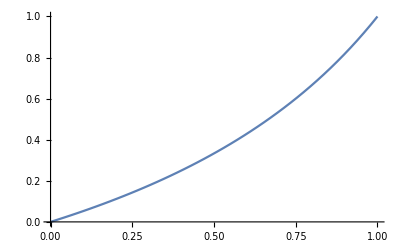

```mathematica
Plot[-e/(-2+e),{e,0,1}]
```

```mathematica
1/(2n)+1/(2n)Q0+(1-1/n)Q1 /.solFstPairs3 /.k->1//FullSimplify

% == (1/(2n)+e/(2k)-e/(4 k n))/(1-(1-1/(2n))((1-m)^2(1-e)+e(1-1/(2k))1/(2k-1))) /.k->1//FullSimplify
```

(-1+e-e n)/(-1+2 (-2+m) m (-1+n)+e^2 (-2+m) m (-1+n)-e (1+3 (-2+m) m) (-1+n))

(-1+e-e n)/(-1+2 (-2+m) m (-1+n)+e^2 (-2+m) m (-1+n)-e (1+3 (-2+m) m) (-1+n))==(2+e (-1+2 n))/(2+e (1+2 (-2+m) m) (-1+2 n)+2 m (-2+m+4 n-2 m n))

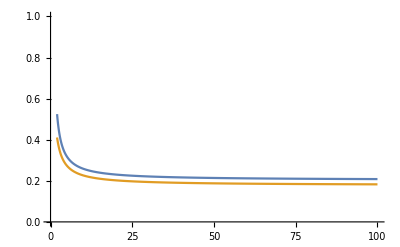

```mathematica
Plot[Evaluate[{1/(2n)+1/(2n)Q0+(1-1/n)Q1 ,(1/(2n)+e/(2k)-e/(4 k n))/(1-(1-1/(2n))((1-m)^2(1-e)+e(1-1/(2k))1/(2k-1))) } /.solFstPairs3/.e->0.3 /.k->1 /.m->.9],{n,2,100},PlotRange->{0,1}]
```

```mathematica
solFstPairs4=Solve[{ 
Q1e ==  1/k (1/2+1/2 Q0Ne),
Q1Ne == (1-m)^2(1/n(1/2+1/2 Q0Ne) + (1-1/n)Q1Ne),

Q0e == 1/k(1/2+1/2 Q0Ne),
Q0Ne ==1/n(1/2+1/2 Q0Ne) + (1-1/n)Q1Ne

},{Q1e,Q1Ne,Q0e,Q0Ne}] //Simplify //Flatten
```

{Q1e→(-1-2 m (-1+n)+m^2 (-1+n))/(k (-1-4 m (-1+n)+2 m^2 (-1+n))),Q1Ne→-(-1+m)^2/(-1-4 m (-1+n)+2 m^2 (-1+n)),Q0e→(-1-2 m (-1+n)+m^2 (-1+n))/(k (-1-4 m (-1+n)+2 m^2 (-1+n))),Q0Ne→1/(1+4 m (-1+n)-2 m^2 (-1+n))}

```mathematica
solFstPairs4 /.k->1 //Simplify
```

{Q1e→(-1-2 m (-1+n)+m^2 (-1+n))/(-1-4 m (-1+n)+2 m^2 (-1+n)),Q1Ne→-(-1+m)^2/(-1-4 m (-1+n)+2 m^2 (-1+n)),Q0e→(-1-2 m (-1+n)+m^2 (-1+n))/(-1-4 m (-1+n)+2 m^2 (-1+n)),Q0Ne→1/(1+4 m (-1+n)-2 m^2 (-1+n))}

```mathematica
1/(2n)+(1-e)(1/(2n)Q0Ne+(1-1/n)Q1Ne) + e (1/(2n)Q0e+(1-1/n)Q1e)  /.solFstPairs4/.α->0/. m-> IC/n/.IC-> 1/. n-> 10 /.k->1 /.e->0.5/.mp->0 //N
```

0.429355

## With pollen dispersal -- before recolonization reproduction -- with inbreeding

```mathematica
Clear["Global`*"];
```

```mathematica
(* mp := Probability that male inherited gene copy is philopatric, assume that seeds that colonize an empty patch reproduce immediately only with local mates; k colonizers per patch from random origin so unrelated *)
```

```mathematica
zEback = (4 e^2 (-1+m) (-1+n) (2+mp (-1+α))+e (-4 (-1+n) (-1+m (2+mp (-1+α))-α)-k (-1+m) (2+mp (-1+α)) (m (-1+n) (2+mp (-1+α)) (1+α)-2 (1+n-α+n α)-mp (-1+n) (-1+α^2)))+k (m^2 (-1+n) (2+mp (-1+α))^2 (1+α)+mp (-1+n) (4+mp (-1+α)) (-1+α^2)-2 m (2+mp (-1+α)) (2 (n-α+n α)+mp (-1+n) (-1+α^2))))/(4 e^2 (-1+m) (-1+n) (2+mp (-1+α))+2 k (mp+m (2+mp (-1+α))-mp α) (2-4 n+m (-1+n) (2+mp (-1+α))+mp (-1+n+α-n α))-2 e (-1+m) (2+mp (-1+α)) (2 (-1+n)+k (-2 n+m (-1+n) (2+mp (-1+α))+mp (-1+n+α-n α)))) ;
```

```mathematica
cm=72/2.54;
```

```mathematica
style=Directive[FontFamily->"Arial",FontSize->12];
blue=RGBColor["#0A71B7"]
orange= RGBColor["#D25F02"]
```

RGBColor[0.0392156862745098, 0.44313725490196076, 0.7176470588235294]

RGBColor[0.8235294117647058, 0.37254901960784315, 0.00784313725490196]

```mathematica
Sqrt[0.1]
```

0.316228

```mathematica
QR[n_]:= 1/n(1/2+1/2 Q0)+(n-1)/n Q1 ;
```

```mathematica
(1/4+1/4(1-backmp (1-α))^2+1/2 (1-backmp (1-α)))  //Simplify
% == (1/2+1/2(1-backmp (1-α)))^2//Simplify
```

1/4 (2+backmp (-1+α))^2

True

```mathematica
solFstPairs3=Solve[{ 
Q0 ==(1-e)( α  (1/2+1/2 Q0) + (1-α) (1-backmp)QR[n])+ e (α  (1/2+1/2 Q0) + (1-α) 1/k(1/2+1/2 Q0)),

Q1 ==(1-e)(1-backm)^2(1/4 QR[n]+1/4(1-backmp (1-α))^2 QR[n]+1/2 (1-backmp (1-α))QR[n])+ e/k  (1/2+1/2 Q0)

},{Q0,Q1}] /. backmp-> ((1-e) mp)/((1-e) mp+(1-mp))/. backm -> ((1-e) m)/((1-e) m+(1-m))//Simplify //Flatten  ;
```

```mathematica
Q1 /.solFstPairs3 /.α->0/. n-> 100/. m-> 1. /.k->1 /.mp-> 0. /. e-> 0.3
```

0.202007

```mathematica
Q1 /.solFstPairs3 /.α->0 /.e->0 ;
Series[%/.m-> M/n/.mp-> Mp/n   ,{n,∞,0}] //FullSimplify //Normal
```

1/(1+4 M+2 Mp)

```mathematica
Q0 /.solFstPairs3  ;
Series[%/.m-> M/n/.mp-> Mp/n   ,{n,∞,0}] //FullSimplify //Normal
```

-1-(2 k)/(1+k (-2+α)-α)

```mathematica
(Q0-Q1)/(1-Q1) /.solFstPairs3  ;
Series[%/.m-> M/n/.mp-> Mp/n   ,{n,∞,0}] //FullSimplify //Normal
```

-α/(-2+α)

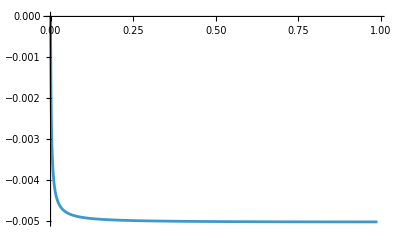

```mathematica
Plot[Evaluate[Q1-Q1/((1-e)(1-backm)^2) /. backm -> ((1-e) m)/((1-e) m+(1-m))/.solFstPairs3 /.e->  0./.α->0/. n-> 100  /.k->1/.mp->0],{m,0,.99},PlotRange->All]
```

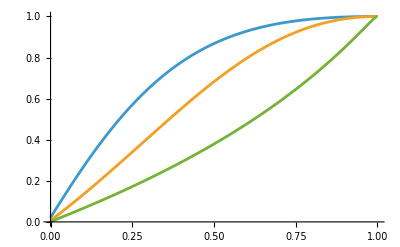

```mathematica
Q1 /.solFstPairs3 /.α->0/. n-> 100/. m-> .1 /.k->1;
Plot[Evaluate[% /.mp->{0,0.3,.99}] ,{e,0,1}]
```

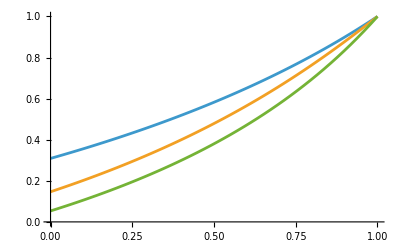

```mathematica
Q0 /.solFstPairs3 /. n-> 100/. m-> .1 /.k->1 /.e->0.1;
Plot[Evaluate[% /.mp->{0,0.3,.99}] ,{α,0,1}]
```

```mathematica
(Q0-Q1)/(1-Q1)/.solFstPairs3 /.α->0 /.mp->0 /.e->0 //Simplify
```

1/(-1+2 n)

```mathematica
NestList[{1/n(1/2+1/2#[[1]])+(n-1)/n#[[2]],(1-m)(1/n(1/2+1/2#[[1]])+(n-1)/n#[[2]])}& /.n->100 /.m-> .1,{0,0},100]//N
```

{{0.,0.},{0.005,0.0045},{0.00948,0.008532},{0.0134941,0.0121447},{0.0170907,0.0153816},{0.0203133,0.0182819},{0.0232007,0.0208806},{0.0257878,0.023209},{0.0281059,0.0252953},{0.0301829,0.0271646},{0.0320439,0.0288395},{0.0337113,0.0303402},{0.0352053,0.0316848},{0.036544,0.0328896},{0.0377434,0.0339691},{0.0388181,0.0349363},{0.039781,0.0358029},{0.0406438,0.0365794},{0.0414168,0.0372751},{0.0421095,0.0378985},{0.0427301,0.0384571},{0.0432862,0.0389575},{0.0437844,0.039406},{0.0442308,0.0398077},{0.0446308,0.0401677},{0.0449892,0.0404903},{0.0453103,0.0407793},{0.0455981,0.0410383},{0.0458559,0.0412703},{0.0460869,0.0414782},{0.0462938,0.0416644},{0.0464793,0.0418313},{0.0466454,0.0419809},{0.0467943,0.0421149},{0.0469277,0.0422349},{0.0470472,0.0423425},{0.0471543,0.0424389},{0.0472503,0.0425252},{0.0473362,0.0426026},{0.0474133,0.0426719},{0.0474823,0.0427341},{0.0475441,0.0427897},{0.0475995,0.0428396},{0.0476492,0.0428843},{0.0476937,0.0429243},{0.0477335,0.0429602},{0.0477692,0.0429923},{0.0478012,0.0430211},{0.0478299,0.0430469},{0.0478556,0.04307},{0.0478786,0.0430908},{0.0478992,0.0431093},{0.0479177,0.0431259},{0.0479343,0.0431408},{0.0479491,0.0431542},{0.0479624,0.0431662},{0.0479743,0.0431769},{0.047985,0.0431865},{0.0479945,0.0431951},{0.0480031,0.0432028},{0.0480108,0.0432097},{0.0480177,0.0432159},{0.0480238,0.0432214},{0.0480294,0.0432264},{0.0480343,0.0432309},{0.0480387,0.0432349},{0.0480427,0.0432384},{0.0480463,0.0432416},{0.0480495,0.0432445},{0.0480523,0.0432471},{0.0480549,0.0432494},{0.0480572,0.0432514},{0.0480592,0.0432533},{0.0480611,0.043255},{0.0480627,0.0432564},{0.0480642,0.0432578},{0.0480655,0.043259},{0.0480667,0.04326},{0.0480678,0.043261},{0.0480687,0.0432618},{0.0480696,0.0432626},{0.0480703,0.0432633},{0.048071,0.0432639},{0.0480716,0.0432645},{0.0480722,0.043265},{0.0480727,0.0432654},{0.0480731,0.0432658},{0.0480735,0.0432662},{0.0480739,0.0432665},{0.0480742,0.0432668},{0.0480745,0.043267},{0.0480747,0.0432673},{0.048075,0.0432675},{0.0480752,0.0432676},{0.0480753,0.0432678},{0.0480755,0.043268},{0.0480757,0.0432681},{0.0480758,0.0432682},{0.0480759,0.0432683},{0.048076,0.0432684},{0.0480761,0.0432685}}

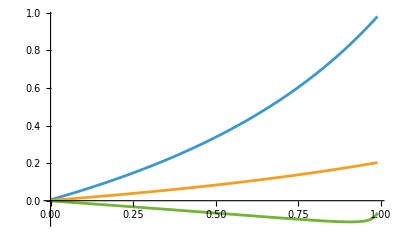

```mathematica
Plot[Evaluate[(Q0-Q1)/(1-Q1)/.solFstPairs3 /.α->0./. n-> 100/. m-> .1 /.k->1/.mp->{0,0.3,.99}],{e,0,.99}]
```

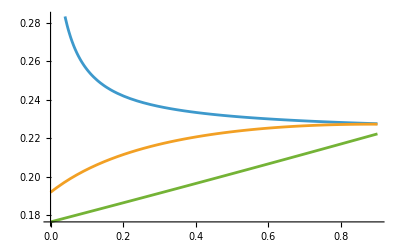

```mathematica
Plot[Evaluate[Q0/.solFstPairs3 /.α->0.3/. n-> 100/. m-> .01 /.k->10/.mp->{0,0.3,.99}],{e,0,.9}]
```

```mathematica
FST == Q1;
FIS ==(Q0-Q1)/(1-Q1);
FIT == Q0 ;
(* See Rousset p. 18 *)
```

```mathematica
zbar = (zi + zj+(n-2)z0)/n;
localseeds = f n zbar (* also equal to ovules *);
paraseeds = f n z ;
```

```mathematica
(* fitness through male function *)
wmale = (1-e)n ( (α zi f+(1-α)localseeds ((1-mp) (1-zi))/(n (1-mp) (1-zbar)+ n  (1-e)mp (1-z)) )( (1-m)/((1-m)localseeds+ m (1-e)paraseeds) +((1-e)m)/((1-m)paraseeds+ m (1-e)paraseeds)+(e m)/(m (1-e)paraseeds) )+  (1-e)(1-α)paraseeds  (mp(1-zi))/(n (1-mp) (1-z)+ n  (1-e)mp (1-z))(  (1-m)/((1-m)paraseeds+ m (1-e)paraseeds)+((1-e)m)/((1-m)paraseeds+ m (1-e)paraseeds) + (e m)/(m (1-e)paraseeds)  ) ) ;
(* fitness through female function *)
wfemale = (1-e)n ( ((1-m) f zi)/((1-m)localseeds+ m (1-e)paraseeds) + m (1-e)(f zi)/((1-m)paraseeds+ m (1-e)paraseeds) + m e (f zi)/(m (1-e)paraseeds)) ;

monopop = {zi-> z,zj-> z,z0->z}
```

{zi→z,zj→z,z0→z}

```mathematica
wmale/.monopop //Simplify
wfemale/.monopop //Simplify
```

1

1

```mathematica
w =1/2( wmale+ wfemale );
```

```mathematica
D[w,zi]+ (n-1)D[w,zj]+D[w,z]/.monopop  //Simplify
```

0

```mathematica
D[w,zi] /.r-> (2Q1)/(1+Q0) /.monopop  /. solFstPairs3 ;
soln3Direct=Flatten@Solve[%==0,z] //Simplify
```

{z→((-1+e mp) (-2 m (2+mp (-1+α))+m^2 (2+mp (-1+α))-(-1+n) (1+α)+e^3 m^2 mp n (1+α)+e^2 (mp (1+α)-2 m mp (1+n) (1+α)+m^2 (-1+2 mp+α-n (1+α)))+e (-2-2 m^2 (1+mp α)+mp (n-2 α+n α)+2 m (3+n-α+n α+mp (-1+3 α)))))/(-2+2 mp-mp^2+2 n+2 e^4 m^2 mp^2 n+2 m (2+mp (-1+α))-2 mp α+mp^2 α+m^2 (-2+mp-mp α)+e^3 mp (mp (1+α)+m^2 (-1+2 mp-4 n+α)-2 m mp (1+2 n+α))-e^2 (-2 m^2 n+mp^2 (-2 n+m (2-6 α)+2 α+m^2 (1+α))+mp (3-8 m (1+n)+α+2 m^2 (1+α)))+e (2+mp-4 mp n+3 mp α+m^2 (2+mp^2 (-1+α)+2 mp (1+α))-2 m (2 (1+n)+2 mp^2 (-1+α)+mp (3+α))))}

```mathematica
D[w,zj] /.r-> (2Q1)/(1+Q0) /.monopop  /. solFstPairs3 ;
soln3Indirect=Flatten@Solve[%==0,z] //Simplify
```

{z→((-1+e mp) (1-2 m (2+mp (-1+α))+m^2 (2+mp (-1+α))+α+e^2 (mp (1+α)-2 m mp (1+α)+m^2 (-1+2 mp+α))-2 e (1+mp α+m (-3+mp+α-3 mp α)+m^2 (1+mp α))))/((-1+e) (2+mp^2 (1+e-α-e α+e^2 (1+α))-mp (2-2 α+e (3+α))-2 m (2+mp (-1-4 e+α)+e mp^2 (2+e-2 α+e α))+m^2 (2+e mp^2 (1+2 e-α)+mp (-1+e^2 (-1+α)+α-e (3+α)))))}

```mathematica
D[w,zi]+ (n-1)r D[w,zj]/.r-> (2Q1)/(1+Q0) /.monopop  /. solFstPairs3 ;
soln3=Flatten@Solve[%==0,z] //Simplify
```

{z→(k (-mp (-1+n) (4+mp (-1+α)) (-1+α^2)+2 m (2+mp (-1+α)) (2 (1+n-α+n α)+mp (-1+n) (-1+α^2))-m^2 (2+mp (-1+α)) (2 (1+n-α+n α)+mp (-1+n) (-1+α^2)))+4 e^4 mp (mp (-1+n) (1+α)-2 m mp (-1+n) (1+α)+m^2 ((-1+n) (-1+α)+mp (-2+n (2+k+k α))))+e (-4 (-1+n) (1-2 m (2+mp (-1+α))+m^2 (2+mp (-1+α))+α)+k (4 (1+n-α+n α)+mp^2 (-1+n) (-1-3 α+α^2+3 α^3)+4 mp (-1+α) (-1-2 α+2 n (1+α))+m^2 (8 mp (1+α) (1+(-1+n) α)+4 (1+n-α+n α)+mp^2 (-1+α) (3+n-4 α+4 n α-3 α^2+3 n α^2))-2 m (8 (1+n-α+n α)+4 mp (1+α+2 n α+2 (-1+n) α^2)+mp^2 (-1+α) (3+n-4 α+4 n α-3 α^2+3 n α^2))))+e^3 (mp (-4 (-1+n) (3+α+2 mp α)+k mp (1+α) (3-2 α-α^2+n (1+α)^2))-2 m mp (-16 (-1+n)+4 mp (-1+n+3 α-3 n α)+k mp (1+α) (3-2 α-α^2+n (5+2 α+α^2)))+m^2 (4 (-1+n+α-n α)-4 mp (k+4 (-1+n)-k α+2 k n (1+α))+mp^2 (-8 (-1+n) α+k (7-3 α-3 α^2-α^3+n (1+α)^3))))-e^2 (8-8 n+k mp^2 (-1+α) (-1-8 α-3 α^2+n (5+8 α+3 α^2))+4 mp (-((-1+n) (1+3 α))+k (2-α-α^2+n (1+α)^2))-2 m (4 (-1+n) (-3+α)+4 mp (-((-1+n) (1+3 α))+k (3+α) (1+n-α+n α))+mp^2 (4 (-1+n+α-n α)+k (-1+3 α) (3-2 α-α^2+n (1+α)^2)))+m^2 (-4 (-1+n) (2+mp^2 (-1+α)+2 mp (1+α))+k (-4 (1+n-α+n α)+4 mp (3-2 α-α^2+n (1+α)^2)+mp^2 (1+7 α-5 α^2-3 α^3+n (1+α)^2 (-1+3 α))))))/(2 (-k (-2 m (2+mp (-1+α)) (2 n+mp (-1+n) (-1+α))+m^2 (2+mp (-1+α)) (2 n+mp (-1+n) (-1+α))+mp (4 n+mp (-1+n (-1+α)-α)) (-1+α))+2 e^4 mp (m^2 (2 mp (-1+n+k n)+(-1+n) (-1+α))+mp (-1+n) (1+α)-2 m mp (-1+n) (1+α))-e^2 (4-4 n+2 mp (k-k α+2 k n (1+α)-(-1+n) (1+3 α))+k mp^2 (-1+α) (-1-3 α+n (5+3 α))-2 m (4-4 n-2 mp (-1+n) (3+α)+4 k mp (1-α+n (3+α))+mp^2 (4 (-1+n+α-n α)+k (-1+3 α) (1+n-α+n α)))+m^2 (-4 (-1+n+k n)+4 mp (1+(-1+k) n) (1+α)+mp^2 (2 (-1+n+α-n α)+k (1+α) (3-n-3 α+3 n α))))+e (4-4 n+4 k n+2 mp (2-2 n+k (-1+4 n)) (-1+α)+mp^2 (-1+n) (-1+α) (2+k+3 k α)-2 m (4+(-4+8 k) n+k mp^2 (-1+α) (3+n-3 α+3 n α)+2 mp (-1+n+α-n α+k (3-3 α+4 n α)))+m^2 (4+4 (-1+k) n+k mp^2 (-1+α) (1+n-3 α+3 n α)+2 mp (-1+n+α-n α+k (2-2 α+4 n α))))+e^3 mp (-2 (-1+n) (3+α+2 mp α)+k mp (1+α) (1+n-α+n α)-2 m (8-8 n+mp (k-k α^2-2 (-1+n) (-1+3 α)+k n (5+2 α+α^2)))+m^2 (-2 (2+mp) (-1+n) (1+α)+k (-2-8 n+2 α+mp (3-2 α-α^2+n (1+α)^2))))))}

```mathematica
z /. soln3  /. e->0 /.mp->0;
% ==1/2(1+ α +1/n (1-α))//Simplify
```

True

```mathematica
z /. soln3 /. e->0.333 /.k-> 1 /. n-> 100 /. m-> 0.1 /. α-> 0 /. mp-> 0//Simplify
```

0.809796

0.505+0.495 α

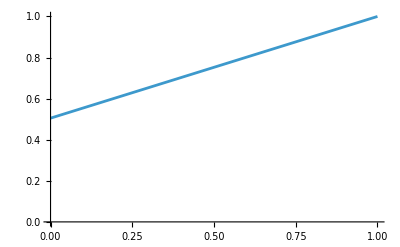

```mathematica
z /. soln3  /. e->0. /.k-> n /. n-> 100 /. m-> 1/100 /. mp-> 0//Simplify
Plot[%,{α,0,1},PlotRange->{0,1} ]
```

(99 e^3+20099 k+e^2 (1920798+101 k)+e (-950598+969701 k))/(2 (19900 k+e^2 (970299+100 k)+e (-970299+960100 k)))

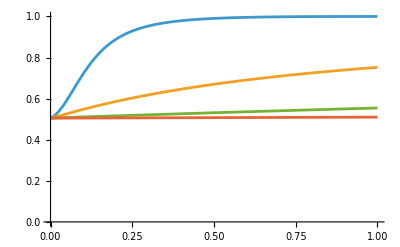

```mathematica
z /. soln3  /.α-> 0 /. n-> 100 /. m-> 1/100 /. mp-> 0//Simplify
Plot[Evaluate[  % /.k-> {1,2,10,100} ] ,{e,0,1},PlotRange->{0,1} ]
```

(1.04836-0.809174 mp+0.0801543 mp^2)/(1.05846+0.707422 mp-1. mp^2)

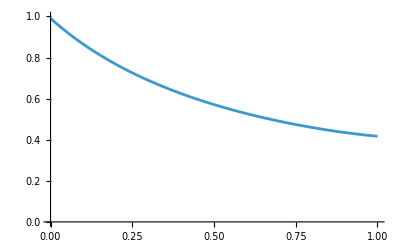

```mathematica
z /. soln3  /. e->0.5 /.k-> 1 /.  α-> 0  /. n-> 100 /. m-> 1/100 //Simplify
Plot[%,{mp,0,1},PlotRange->{0,1} ]
```

```mathematica
1
```

```mathematica
z /. soln3   /.mp->0  ;
Series[%  /. m-> M/n,{n,∞,0}] //FullSimplify //Normal ;
% ==1/2(1+ α +e/(e+k-1)(1-α))//Simplify
```

True

```mathematica
LogLinearPlot[Evaluate[z /. soln3 /. n-> 100/. m-> 0.1/.k->{1,2,3} /.mp->0.0 /.α-> 0. /. e->1/(1+Nt)],{Nt,1,100},PlotRange->{0.4,1},AxesOrigin->{1,0.5},Frame-> True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],PlotStyle->{GrayLevel[0],GrayLevel[0.5],GrayLevel[0.7]},ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5] 
(* Export["/Users/cmullon/Dropbox/Projects/SexAllocation/PlotZExt1BackD.pdf",%,Background->None]; *)
```

-Graphics-

```mathematica
LogLinearPlot[Evaluate[z /. soln3 /. n-> 100/. m-> 0.1/.k->2 /.mp->0.0 /.α-> {0.,0.1,0.2} /. e->1/(1+Nt)],{Nt,1,100},PlotRange->{0.4,1},AxesOrigin->{1,0.5},Frame-> True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],PlotStyle->{GrayLevel[0],GrayLevel[0.5],GrayLevel[0.7]},ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5]
(* Export["/Users/cmullon/Dropbox/Projects/SexAllocation/PlotZExt2BackD.pdf",%,Background->None]; *)
```

-Graphics-

```mathematica
z /. soln3     ;
Series[%  /. m->m δ/.mp-> mp δ  /. e-> e δ/. α-> α δ /. n-> n/δ ,{δ,0,1}] //FullSimplify//Normal   ;
%  == 1/2(1+α+((e+2 m-mp) (n e +k))/(n(e (k-1)+ (2 m+mp)k)))  /.δ->1//FullSimplify
```

True

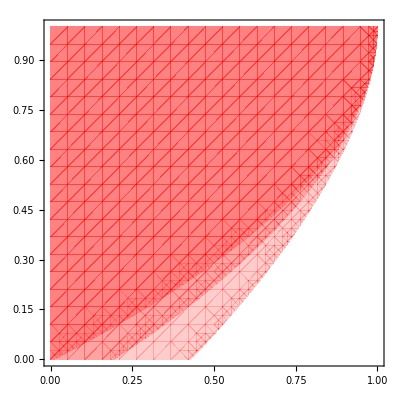

```mathematica
RegionPlot[Evaluate[Table[z>1/2/. soln3 /. n-> 100 /.k->1 /. e->1/(1+Nt)/. α->0.,{Nt,{2,5,100}}]],{mp,0,1},{m,0,1},LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,PlotStyle->Directive[Red,Opacity[0.2]],BoundaryStyle->None]
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/PlotContour1BackD.pdf",%,Background->None];
```

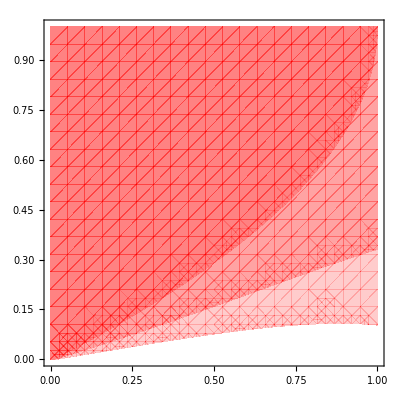

```mathematica
RegionPlot[Evaluate[Table[z>1/2/. soln3 /. n-> 100 /.k->1 /. e->1/(1+100),{α,{0.,0.005,0.01}}]],{mp,0,1},{m,0,1},LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,PlotStyle->Directive[Red,Opacity[0.2]],BoundaryStyle->None]
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/PlotContour2BackD.pdf",%,Background->None];
```

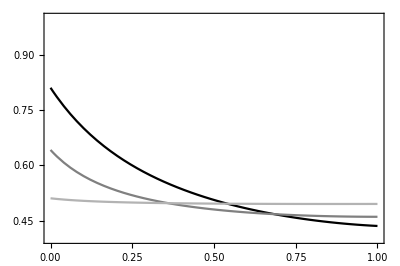

```mathematica
Plot[Evaluate[z /. soln3 /. n-> 100 /.k->1 /. e->1/(1+Nt)/. Nt-> {2,5,100}/. α->0 /. m-> 0.1],{mp,0,1},PlotRange->{0.4,1},AxesOrigin->{1,0.5},Frame-> True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],PlotStyle->{GrayLevel[0],GrayLevel[0.5],GrayLevel[0.7]},ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5]
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/PlotZEquiSeedBackDisp1.pdf",%,Background->None];
```

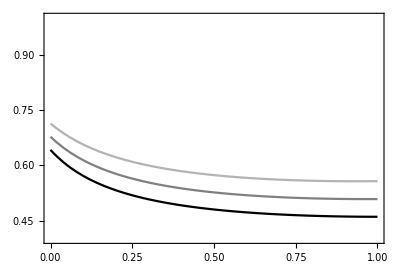

```mathematica
Plot[Evaluate[z /. soln3 /. n-> 100 /.k->1 /. e->1/(1+Nt)/. Nt->5/. α->{0,0.1,0.2} /. m-> 0.1],{mp,0,1},PlotRange->{0.4,1},AxesOrigin->{1,0.5},Frame-> True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],PlotStyle->{GrayLevel[0],GrayLevel[0.5],GrayLevel[0.7]},ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5]
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/PlotZEquiSeedBackDisp2.pdf",%,Background->None];
```

```mathematica
Sum[(t) e (1-e)^t,{t,1,∞}]
Solve[(1-e)/e ==Nt ,e]
```

(1-e)/e

{{e→1/(1+Nt)}}

```mathematica
1/(1+Nt) /.Nt->{1,2,5,10,100} //N
```

{0.5,0.333333,0.166667,0.0909091,0.00990099}

```mathematica
{z,zEback} /. soln3 /. n-> 10/. m-> 0.2/.k->1/.mp->0.1 /.α-> 0.3 /. e->0.5
```

{0.873654,0.840459}

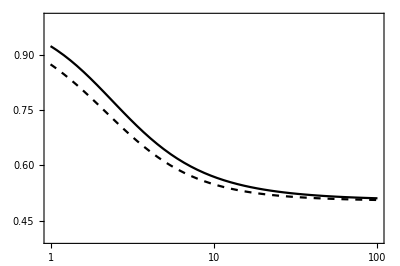

```mathematica
LogLinearPlot[Evaluate[Flatten[{z,zEback} /. soln3 /. n-> 100/. m-> 0.1/.k->1 /.mp->0. /.α-> 0. /. e->1/(1+Nt)]],{Nt,1,100},PlotRange->{0.4,1},AxesOrigin->{1,0.5},Frame-> True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],PlotStyle->{Directive[GrayLevel[0]],Directive[GrayLevel[0],Dashed]},ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5]
(* Export["/Users/cmullon/Dropbox/Projects/SexAllocation/PlotZExt1.pdf",%,Background->None];*)
```

```mathematica
sims=Table[
{z,zEback}  /. soln3/.k->  RandomChoice[{1,2,3,4,5,6}]/. n-> 1000 /. m->  RandomReal[{0,0.1}]   /. e->RandomReal[{0.005,.5}]   /.mp ->RandomReal[{0,.1}]  /. α-> RandomReal[{0.,1.}]
,{i,1000}];
```

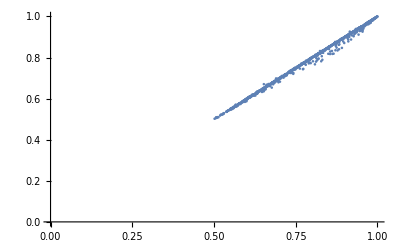

```mathematica
ListPlot[sims,PlotRange->{{0,1},{0,1}}]
```

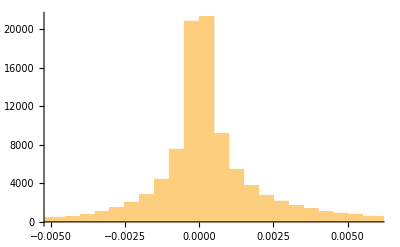

```mathematica
data=Table[
{k,m,e,mp,α,z-zEback } /. soln3/.k->  RandomChoice[{1,2,3,4,5,6}]/. n-> 1000 /. m->  RandomReal[{0,1}]   /. e->RandomReal[{0.,.5}]   /.mp ->RandomReal[{0,1}]  /. α-> RandomReal[{0.,1.}]
,{i,100000}] ;
Histogram[data[[All,6]]]
```

```mathematica
lm=LinearModelFit[data,{k,m,e,mp,α},{k,m,e,mp,α}]
```

FittedModel[0.00267931+0.00377796 e-0.000130727 k+0.00160656 m-0.00408662 mp-0.00285437 α]

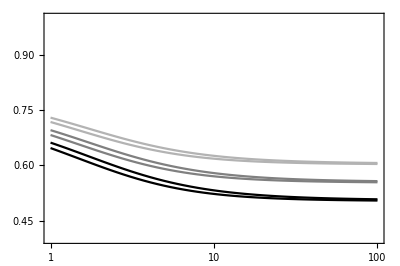

```mathematica
LogLinearPlot[Evaluate[{z,zEback} /. soln3 /. n-> 100/. m-> 0.1/.k->2 /.mp->0.0 /.α-> {0.,0.1,0.2} /. e->1/(1+Nt)],{Nt,1,100},PlotRange->{0.4,1},AxesOrigin->{1,0.5},Frame-> True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],PlotStyle->{GrayLevel[0],GrayLevel[0.5],GrayLevel[0.7]},ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5]
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/PlotZExt2.pdf",%,Background->None];
```

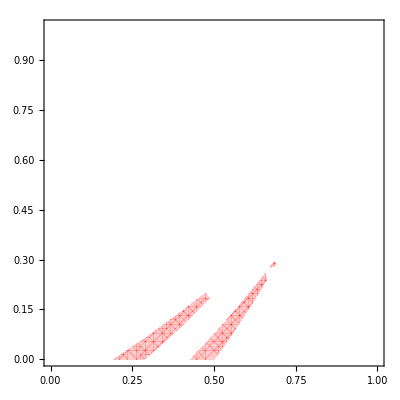

```mathematica
RegionPlot[Evaluate[Table[{ z<1/2  && zEback >1/2} /. soln3 /. n-> 100 /.k->1 /. e->1/(1+Nt)/. α->0.,{Nt,{2,5,100}}]],{mp,0,1},{m,0,1},LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,PlotStyle->Directive[Red,Opacity[0.2]],BoundaryStyle->None]
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/PlotContour1.pdf",%,Background->None];
```

```mathematica
RegionPlot[Evaluate[Table[z>1/2/. soln3 /. n-> 100 /.k->1 /. e->1/(1+100),{α,{0.,0.005,0.01}}]],{mp,0,1},{m,0,1},LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,PlotStyle->Directive[Red,Opacity[0.2]],BoundaryStyle->None]
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/PlotContour2.pdf",%,Background->None];
```

-Graphics-

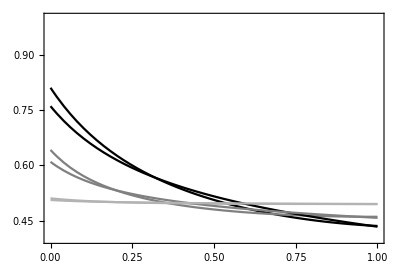

```mathematica
Plot[Evaluate[{z,zEback} /. soln3 /. n-> 100 /.k->1 /. e->1/(1+Nt)/. Nt-> {2,5,100}/. α->0 /. m-> 0.1],{mp,0,1},PlotRange->{0.4,1},AxesOrigin->{1,0.5},Frame-> True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],PlotStyle->{GrayLevel[0],GrayLevel[0.5],GrayLevel[0.7]},ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5]
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/PlotZEquiSeedDisp1.pdf",%,Background->None];
```

```mathematica
Plot[Evaluate[z /. soln3 /. n-> 100 /.k->1 /. e->1/(1+Nt)/. Nt->5/. α->{0,0.1,0.2} /. m-> 0.1],{mp,0,1},PlotRange->{0.4,1},AxesOrigin->{1,0.5},Frame-> True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],PlotStyle->{GrayLevel[0],GrayLevel[0.5],GrayLevel[0.7]},ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5]
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/PlotZEquiSeedDisp2.pdf",%,Background->None];
```

-Graphics-

```mathematica
sims=Table[
{(Q0-Q1)/(1-Q1),Q0,Q1,z}/. solFstPairs3 /. soln3/.k->  RandomChoice[{1,2,3,4,5,6}]/. n-> 100 /. m->  RandomReal[{0,0.1}]   /. e->RandomReal[{0.005,.5}]   /.mp ->RandomReal[{0,.1}]  /. α-> RandomReal[{0.,1.}]
,{i,500}];
```

```mathematica
ListPlot[ sims[[All,{4,1}]] ,Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Black,Thickness[0.1],Circle[]},ImageSize->5],PlotRange->{{.5,1},{0,1}}] 
ListPlot[ sims[[All,{4,2}]] ,Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Black,Thickness[0.1],Circle[]},ImageSize->5],PlotRange->{{.5,1},{0,1}}] 
ListPlot[ sims[[All,{4,3}]] ,Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Black,Thickness[0.1],Circle[]},ImageSize->5],PlotRange->{{.5,1},{0,1}}]
```

```mathematica
sims1=Table[
{(Q0-Q1)/(1-Q1),Q0,Q1,z,"fullModel"} /. solFstPairs3 /. soln3/.k->  RandomChoice[{1,2,3,4,5,6}]/. n-> 1000 /. m->  RandomReal[{0,0.1}]   /. e->RandomReal[{0.005,.5}]   /.mp ->RandomReal[{0,.1}]  /. α-> RandomReal[{0.,1.}]
,{i,500}];
sims2=Table[
{(Q0-Q1)/(1-Q1),Q0,Q1,z, "randomMating"} /. solFstPairs3 /. soln3/.k->  RandomChoice[{1,2,3,4,5,6}]/. n-> 1000 /. m->  RandomReal[{0,0.1}]   /. e->RandomReal[{0.005,.5}]   /.mp ->RandomReal[{0,.1}]  /. α-> 0.0
,{i,500}];
sims3=Table[
{(Q0-Q1)/(1-Q1),Q0,Q1,z,"randomMatingNoPolenDisp"} /. solFstPairs3 /. soln3/.k->  RandomChoice[{1,2,3,4,5,6}]/. n-> 1000 /. m->  RandomReal[{0,0.1}]   /. e->RandomReal[{0.005,.5}]   /.mp ->0.0  /. α-> 0.0
,{i,500}];
Export["~/Downloads/Sims.csv", Join[sims1,Rest[sims2],Rest[sims3]]]
```

~/Downloads/Sims.csv

```mathematica
simsImport=Import["/Users/cmullon/Dropbox/Projects/SexAllocation/Sims.csv"];
```

```mathematica
samples = 500;
```

```mathematica
data=simsImport[[All,{4,1}]] ;
dataPlot=RandomSample[simsImport[[All,{4,1}]],samples] ;
p11=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p12=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p1 = Show[p11,p12] ;

data=simsImport[[All,{4,2}]] ;
dataPlot=RandomSample[simsImport[[All,{4,2}]],samples] ;
p21=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p22=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p2 = Show[p21,p22] ;

data=simsImport[[All,{4,3}]] ;
dataPlot=RandomSample[simsImport[[All,{4,3}]],samples] ;
p31=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p32=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p3 = Show[p31,p32] ;
```

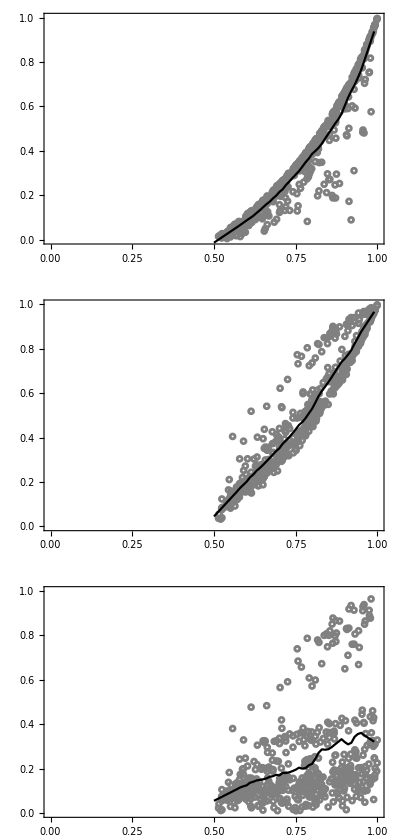

```mathematica
GraphicsColumn[{p1,p2,p3}]
```

```mathematica
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/AssoF.pdf",%]
```

/Users/cmullon/Dropbox/Projects/SexAllocation/AssoF.pdf

```mathematica
sims2=Table[
{(Q0-Q1)/(1-Q1),Q0,Q1,z}/. solFstPairs3 /. soln3/.k->  RandomChoice[{1,2,3,4,5,6}]/. n-> 1000 /. m->  RandomReal[{0,0.1}]   /. e->RandomReal[{0.005,.5}]   /.mp ->0  /. α-> 0
,{i,500}];
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/SimsRandomMating.csv",sims2]
```

/Users/cmullon/Dropbox/Projects/SexAllocation/SimsRandomMating.csv

```mathematica
simsImport2=Import["/Users/cmullon/Dropbox/Projects/SexAllocation/SimsRandomMating.csv"];
```

```mathematica
data=simsImport2[[All,{4,1}]] ;
dataPlot=RandomSample[simsImport2[[All,{4,1}]],samples] ;
p11=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p12=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p1 = Show[p11,p12] ;

data=simsImport2[[All,{4,2}]] ;
dataPlot=RandomSample[simsImport2[[All,{4,2}]],samples] ;
p21=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p22=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p2 = Show[p21,p22] ;

data=simsImport2[[All,{4,3}]] ;
dataPlot=RandomSample[simsImport2[[All,{4,3}]],samples] ;
p31=ListPlot[dataPlot,PlotRange->{{0,1},{0,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p32=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p3 = Show[p31,p32] ;
```

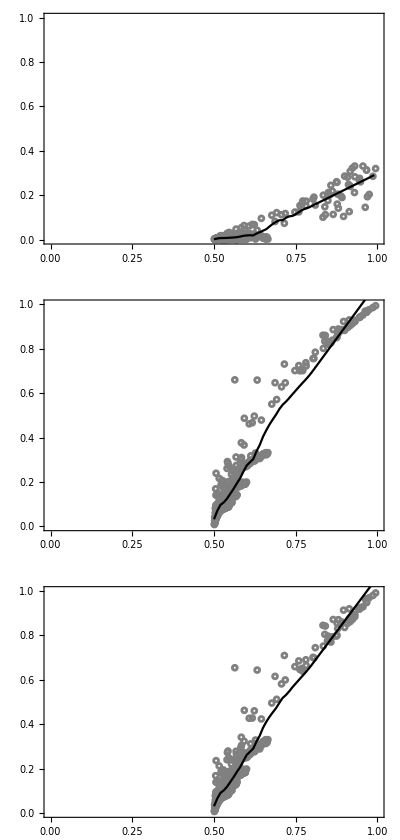

```mathematica
GraphicsColumn[{p1,p2,p3}]
```

```mathematica
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/AssoFRandomMating.pdf",%]
```

/Users/cmullon/Dropbox/Projects/SexAllocation/AssoFRandomMating.pdf

```mathematica
sims3=Table[
{(Q0-Q1)/(1-Q1),Q0,Q1,z}/. solFstPairs3 /. soln3/.k->  RandomChoice[{1,2,3,4,5,6}]/. n-> 1000 /. m->  RandomReal[{0,0.1}]   /. e->RandomReal[{0.005,.5}]   /.mp ->RandomReal[{0,.1}]  /. α->0 
,{i,500}];
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/SimsRandomMatingPollenDisp.csv",sims3]
```

/Users/cmullon/Dropbox/Projects/SexAllocation/SimsRandomMatingPollenDisp.csv

```mathematica
simsImport3=Import["/Users/cmullon/Dropbox/Projects/SexAllocation/SimsRandomMatingPollenDisp.csv"];
```

```mathematica
data=simsImport3[[All,{4,1}]] ;
dataPlot=RandomSample[simsImport3[[All,{4,1}]],samples] ;
p11=ListPlot[dataPlot,PlotRange->{{0,1},{-1,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p12=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p1 = Show[p11,p12] ;

data=simsImport3[[All,{4,2}]] ;
dataPlot=RandomSample[simsImport3[[All,{4,2}]],samples] ;
p21=ListPlot[dataPlot,PlotRange->{{0,1},{-1,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p22=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p2 = Show[p21,p22] ;

data=simsImport3[[All,{4,3}]] ;
dataPlot=RandomSample[simsImport3[[All,{4,3}]],samples] ;
p31=ListPlot[dataPlot,PlotRange->{{0,1},{-1,1}},Frame->True,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black],ImageSize->{Automatic,7.5cm},FrameTicks->Automatic,AspectRatio-> 1/1.5,Axes->False,PlotMarkers-> Graphics[{Gray,Thickness[0.1],Circle[]},ImageSize->5]] ;
p32=ListPlot[Table[{x,Loess[data,Scaled[0.2],x]},{x,0.5,.99,0.01}],Joined->True,PlotStyle->Black] ;
p3 = Show[p31,p32] ;
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

RandomSample::lrwl: The set of items to sample from, Symbol[], should be a non-empty list or a rule weights -> choices.

RandomSample::lrwl: The set of items to sample from, False, should be a non-empty list or a rule weights -> choices.

ListPlot::lpn: RandomSample[Symbol[],samples] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[RandomSample[Symbol[],samples],PlotRange→{{0,1},{-1,1}},Frame→True,LabelStyle→Directive[FontFamily→Arial,FontSize→14,color],ImageSize→{Automatic,7.5 cm},FrameTicks→Automatic,AspectRatio→0.666667,Axes→False,PlotMarkers→],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

RandomSample::lrwl: The set of items to sample from, Symbol[], should be a non-empty list or a rule weights -> choices.

RandomSample::lrwl: The set of items to sample from, False, should be a non-empty list or a rule weights -> choices.

ListPlot::lpn: RandomSample[Symbol[],samples] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[RandomSample[Symbol[],samples],PlotRange→{{0,1},{-1,1}},Frame→True,LabelStyle→Directive[FontFamily→Arial,FontSize→14,color],ImageSize→{Automatic,7.5 cm},FrameTicks→Automatic,AspectRatio→0.666667,Axes→False,PlotMarkers→],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

RandomSample::lrwl: The set of items to sample from, Symbol[], should be a non-empty list or a rule weights -> choices.

RandomSample::lrwl: The set of items to sample from, False, should be a non-empty list or a rule weights -> choices.

ListPlot::lpn: RandomSample[Symbol[],samples] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[RandomSample[Symbol[],samples],PlotRange→{{0,1},{-1,1}},Frame→True,LabelStyle→Directive[FontFamily→Arial,FontSize→14,color],ImageSize→{Automatic,7.5 cm},FrameTicks→Automatic,AspectRatio→0.666667,Axes→False,PlotMarkers→],].

```mathematica
GraphicsColumn[{p1,p2,p3}]
```

-Graphics-

```mathematica
Export["/Users/cmullon/Dropbox/Projects/SexAllocation/AssoFRandomMatingPollenDisp.pdf",%]
```

/Users/cmullon/Dropbox/Projects/SexAllocation/AssoFRandomMatingPollenDisp.pdf

```mathematica
data=Table[{Nt,k, α, z/. soln3/. {n->100,m->0.1,mp->0.0,e->1/(1+Nt)}},{Nt,1,100,0.1},{k,1,3}, {α, {0, 0.1, 0.2}}]//Flatten[#,2]&;
header={"Nt","K","SELF","Value"};
dataWithHeader=Prepend[data,header];
Export["~/SexAllocationEvolution/Nt_K_Value_Table.csv",dataWithHeader]
```

~/SexAllocationEvolution/Nt_K_Value_Table.csv

{1,1,0,0.922923,1,1,0.1,0.930631,1,1,0.2,0.938339,1,2,0,0.661236,1,2,0.1,0.695113,1,2,0.2,0.728989,1,3,0,0.601077,1,3,0.1,0.640969,1,3,0.2,0.680861,2,1,0,0.810091,2,1,0.1,0.829082,2,1,0.2,0.848073,2,2,0,0.613033,2,2,0.1,0.651729,2,2,0.2,0.690426,2,3,0,0.570637,2,3,0.1,0.613574,2,3,0.2,0.65651,3,1,0,0.729173,3,1,0.1,0.756255,3,1,0.2,0.783338,3,2,0,0.585638,3,2,0.1,0.627074,3,2,0.2,0.668511,3,3,0,0.554161,3,3,0.1,0.598745,3,3,0.2,0.643329,4,1,0,0.676482,4,1,0.1,0.708834,4,1,0.2,0.741185,4,2,0,0.568584,4,2,0.1,0.611725,4,2,0.2,0.654867,4,3,0,0.544027,4,3,0.1,0.589625,4,3,0.2,0.635222,5,1,0,0.64147,5,1,0.1,0.677323,5,1,0.2,0.713176,5,2,0,0.557151,5,2,0.1,0.601436,5,2,0.2,0.645721,5,3,0,0.537235,5,3,0.1,0.583511,5,3,0.2,0.629788,6,1,0,0.617212,6,1,0.1,0.655491,6,1,0.2,0.69377,6,2,0,0.549038,6,2,0.1,0.594134,6,2,0.2,0.63923,6,3,0,0.532394,6,3,0.1,0.579155,6,3,0.2,0.625916,7,1,0,0.599698,7,1,0.1,0.639728,7,1,0.2,0.679759,7,2,0,0.543019,7,2,0.1,0.588717,7,2,0.2,0.634415,7,3,0,0.528784,7,3,0.1,0.575905,7,3,0.2,0.623027,8,1,0,0.586592,8,1,0.1,0.627933,8,1,0.2,0.669273,8,2,0,0.538396,8,2,0.1,0.584556,8,2,0.2,0.630716,8,3,0,0.525994,8,3,0.1,0.573395,8,3,0.2,0.620795,9,1,0,0.576483,9,1,0.1,0.618834,9,1,0.2,0.661186,9,2,0,0.534743,9,2,0.1,0.581269,9,2,0.2,0.627794,9,3,0,0.523778,9,3,0.1,0.5714,9,3,0.2,0.619022,10,1,0,0.568485,10,1,0.1,0.611636,10,1,0.2,0.654788,10,2,0,0.53179,10,2,0.1,0.578611,10,2,0.2,0.625432,10,3,0,0.521977,10,3,0.1,0.56978,10,3,0.2,0.617582,11,1,0,0.56202,11,1,0.1,0.605818,11,1,0.2,0.649616,11,2,0,0.529357,11,2,0.1,0.576422,11,2,0.2,0.623486,11,3,0,0.520486,11,3,0.1,0.568438,11,3,0.2,0.616389,12,1,0,0.5567,12,1,0.1,0.60103,12,1,0.2,0.64536,12,2,0,0.527321,12,2,0.1,0.574589,12,2,0.2,0.621856,12,3,0,0.519233,12,3,0.1,0.567309,12,3,0.2,0.615386,13,1,0,0.552253,13,1,0.1,0.597028,13,1,0.2,0.641803,13,2,0,0.525592,13,2,0.1,0.573033,13,2,0.2,0.620473,13,3,0,0.518164,13,3,0.1,0.566348,13,3,0.2,0.614531,14,1,0,0.548486,14,1,0.1,0.593638,14,1,0.2,0.638789,14,2,0,0.524107,14,2,0.1,0.571696,14,2,0.2,0.619285,14,3,0,0.517243,14,3,0.1,0.565519,14,3,0.2,0.613794,15,1,0,0.545257,15,1,0.1,0.590732,15,1,0.2,0.636206,15,2,0,0.522818,15,2,0.1,0.570536,15,2,0.2,0.618255,15,3,0,0.516441,15,3,0.1,0.564797,15,3,0.2,0.613153,16,1,0,0.542462,16,1,0.1,0.588216,16,1,0.2,0.63397,16,2,0,0.52169,16,2,0.1,0.569521,16,2,0.2,0.617352,16,3,0,0.515737,16,3,0.1,0.564163,16,3,0.2,0.612589,17,1,0,0.54002,17,1,0.1,0.586018,17,1,0.2,0.632016,17,2,0,0.520694,17,2,0.1,0.568625,17,2,0.2,0.616555,17,3,0,0.515113,17,3,0.1,0.563602,17,3,0.2,0.612091,18,1,0,0.537869,18,1,0.1,0.584082,18,1,0.2,0.630295,18,2,0,0.519809,18,2,0.1,0.567828,18,2,0.2,0.615847,18,3,0,0.514558,18,3,0.1,0.563102,18,3,0.2,0.611646,19,1,0,0.535961,19,1,0.1,0.582365,19,1,0.2,0.628769,19,2,0,0.519017,19,2,0.1,0.567116,19,2,0.2,0.615214,19,3,0,0.514059,19,3,0.1,0.562654,19,3,0.2,0.611248,20,1,0,0.534259,20,1,0.1,0.580833,20,1,0.2,0.627407,20,2,0,0.518305,20,2,0.1,0.566475,20,2,0.2,0.614644,20,3,0,0.51361,20,3,0.1,0.562249,20,3,0.2,0.610888,21,1,0,0.53273,21,1,0.1,0.579457,21,1,0.2,0.626184,21,2,0,0.517661,21,2,0.1,0.565895,21,2,0.2,0.614129,21,3,0,0.513203,21,3,0.1,0.561883,21,3,0.2,0.610563,22,1,0,0.53135,22,1,0.1,0.578215,22,1,0.2,0.62508,22,2,0,0.517076,22,2,0.1,0.565368,22,2,0.2,0.613661,22,3,0,0.512833,22,3,0.1,0.561549,22,3,0.2,0.610266,23,1,0,0.530099,23,1,0.1,0.577089,23,1,0.2,0.624079,23,2,0,0.516542,23,2,0.1,0.564888,23,2,0.2,0.613233,23,3,0,0.512494,23,3,0.1,0.561245,23,3,0.2,0.609995,24,1,0,0.528959,24,1,0.1,0.576063,24,1,0.2,0.623167,24,2,0,0.516053,24,2,0.1,0.564447,24,2,0.2,0.612842,24,3,0,0.512183,24,3,0.1,0.560965,24,3,0.2,0.609747,25,1,0,0.527917,25,1,0.1,0.575125,25,1,0.2,0.622333,25,2,0,0.515603,25,2,0.1,0.564043,25,2,0.2,0.612482,25,3,0,0.511897,25,3,0.1,0.560707,25,3,0.2,0.609518,26,1,0,0.52696,26,1,0.1,0.574264,26,1,0.2,0.621568,26,2,0,0.515188,26,2,0.1,0.563669,26,2,0.2,0.612151,26,3,0,0.511633,26,3,0.1,0.560469,26,3,0.2,0.609306,27,1,0,0.526079,27,1,0.1,0.573471,27,1,0.2,0.620863,27,2,0,0.514804,27,2,0.1,0.563324,27,2,0.2,0.611844,27,3,0,0.511388,27,3,0.1,0.560249,27,3,0.2,0.60911,28,1,0,0.525265,28,1,0.1,0.572739,28,1,0.2,0.620212,28,2,0,0.514448,28,2,0.1,0.563004,28,2,0.2,0.611559,28,3,0,0.51116,28,3,0.1,0.560044,28,3,0.2,0.608928,29,1,0,0.524511,29,1,0.1,0.57206,29,1,0.2,0.619609,29,2,0,0.514117,29,2,0.1,0.562705,29,2,0.2,0.611294,29,3,0,0.510948,29,3,0.1,0.559853,29,3,0.2,0.608759,30,1,0,0.52381,30,1,0.1,0.571429,30,1,0.2,0.619048,30,2,0,0.513808,30,2,0.1,0.562427,30,2,0.2,0.611046,30,3,0,0.51075,30,3,0.1,0.559675,30,3,0.2,0.6086,31,1,0,0.523158,31,1,0.1,0.570842,31,1,0.2,0.618526,31,2,0,0.513519,31,2,0.1,0.562167,31,2,0.2,0.610815,31,3,0,0.510565,31,3,0.1,0.559509,31,3,0.2,0.608452,32,1,0,0.522548,32,1,0.1,0.570294,32,1,0.2,0.618039,32,2,0,0.513249,32,2,0.1,0.561924,32,2,0.2,0.610599,32,3,0,0.510391,32,3,0.1,0.559352,32,3,0.2,0.608313,33,1,0,0.521978,33,1,0.1,0.56978,33,1,0.2,0.617583,33,2,0,0.512995,33,2,0.1,0.561695,33,2,0.2,0.610396,33,3,0,0.510228,33,3,0.1,0.559205,33,3,0.2,0.608183,34,1,0,0.521444,34,1,0.1,0.569299,34,1,0.2,0.617155,34,2,0,0.512756,34,2,0.1,0.56148,34,2,0.2,0.610205,34,3,0,0.510075,34,3,0.1,0.559067,34,3,0.2,0.60806,35,1,0,0.520941,35,1,0.1,0.568847,35,1,0.2,0.616753,35,2,0,0.512531,35,2,0.1,0.561278,35,2,0.2,0.610025,35,3,0,0.50993,35,3,0.1,0.558937,35,3,0.2,0.607944,36,1,0,0.520469,36,1,0.1,0.568422,36,1,0.2,0.616375,36,2,0,0.512318,36,2,0.1,0.561086,36,2,0.2,0.609855,36,3,0,0.509793,36,3,0.1,0.558814,36,3,0.2,0.607834,37,1,0,0.520023,37,1,0.1,0.568021,37,1,0.2,0.616018,37,2,0,0.512117,37,2,0.1,0.560906,37,2,0.2,0.609694,37,3,0,0.509663,37,3,0.1,0.558697,37,3,0.2,0.607731,38,1,0,0.519602,38,1,0.1,0.567642,38,1,0.2,0.615682,38,2,0,0.511927,38,2,0.1,0.560734,38,2,0.2,0.609542,38,3,0,0.509541,38,3,0.1,0.558587,38,3,0.2,0.607632,39,1,0,0.519204,39,1,0.1,0.567283,39,1,0.2,0.615363,39,2,0,0.511747,39,2,0.1,0.560572,39,2,0.2,0.609397,39,3,0,0.509424,39,3,0.1,0.558482,39,3,0.2,0.607539,40,1,0,0.518827,40,1,0.1,0.566944,40,1,0.2,0.615061,40,2,0,0.511576,40,2,0.1,0.560418,40,2,0.2,0.60926,40,3,0,0.509314,40,3,0.1,0.558382,40,3,0.2,0.607451,41,1,0,0.518469,41,1,0.1,0.566622,41,1,0.2,0.614775,41,2,0,0.511413,41,2,0.1,0.560272,41,2,0.2,0.60913,41,3,0,0.509208,41,3,0.1,0.558287,41,3,0.2,0.607367,42,1,0,0.518129,42,1,0.1,0.566316,42,1,0.2,0.614503,42,2,0,0.511258,42,2,0.1,0.560132,42,2,0.2,0.609006,42,3,0,0.509108,42,3,0.1,0.558197,42,3,0.2,0.607286,43,1,0,0.517806,43,1,0.1,0.566025,43,1,0.2,0.614244,43,2,0,0.51111,43,2,0.1,0.559999,43,2,0.2,0.608888,43,3,0,0.509012,43,3,0.1,0.558111,43,3,0.2,0.60721,44,1,0,0.517498,44,1,0.1,0.565748,44,1,0.2,0.613998,44,2,0,0.510969,44,2,0.1,0.559873,44,2,0.2,0.608776,44,3,0,0.508921,44,3,0.1,0.558029,44,3,0.2,0.607137,45,1,0,0.517204,45,1,0.1,0.565484,45,1,0.2,0.613763,45,2,0,0.510835,45,2,0.1,0.559751,45,2,0.2,0.608668,45,3,0,0.508834,45,3,0.1,0.557951,45,3,0.2,0.607067,46,1,0,0.516924,46,1,0.1,0.565232,46,1,0.2,0.613539,46,2,0,0.510706,46,2,0.1,0.559636,46,2,0.2,0.608565,46,3,0,0.508751,46,3,0.1,0.557876,46,3,0.2,0.607,47,1,0,0.516657,47,1,0.1,0.564991,47,1,0.2,0.613325,47,2,0,0.510583,47,2,0.1,0.559525,47,2,0.2,0.608467,47,3,0,0.508671,47,3,0.1,0.557804,47,3,0.2,0.606937,48,1,0,0.516401,48,1,0.1,0.564761,48,1,0.2,0.613121,48,2,0,0.510465,48,2,0.1,0.559419,48,2,0.2,0.608372,48,3,0,0.508594,48,3,0.1,0.557735,48,3,0.2,0.606875,49,1,0,0.516156,49,1,0.1,0.56454,49,1,0.2,0.612925,49,2,0,0.510352,49,2,0.1,0.559317,49,2,0.2,0.608282,49,3,0,0.508521,49,3,0.1,0.557669,49,3,0.2,0.606817,50,1,0,0.515921,50,1,0.1,0.564329,50,1,0.2,0.612737,50,2,0,0.510244,50,2,0.1,0.559219,50,2,0.2,0.608195,50,3,0,0.50845,50,3,0.1,0.557605,50,3,0.2,0.60676,51,1,0,0.515696,51,1,0.1,0.564126,51,1,0.2,0.612557,51,2,0,0.51014,51,2,0.1,0.559126,51,2,0.2,0.608112,51,3,0,0.508383,51,3,0.1,0.557544,51,3,0.2,0.606706,52,1,0,0.51548,52,1,0.1,0.563932,52,1,0.2,0.612384,52,2,0,0.51004,52,2,0.1,0.559036,52,2,0.2,0.608032,52,3,0,0.508317,52,3,0.1,0.557486,52,3,0.2,0.606654,53,1,0,0.515272,53,1,0.1,0.563745,53,1,0.2,0.612218,53,2,0,0.509943,53,2,0.1,0.558949,53,2,0.2,0.607955,53,3,0,0.508255,53,3,0.1,0.557429,53,3,0.2,0.606604,54,1,0,0.515073,54,1,0.1,0.563566,54,1,0.2,0.612058,54,2,0,0.509851,54,2,0.1,0.558866,54,2,0.2,0.60788,54,3,0,0.508194,54,3,0.1,0.557375,54,3,0.2,0.606556,55,1,0,0.514881,55,1,0.1,0.563393,55,1,0.2,0.611905,55,2,0,0.509761,55,2,0.1,0.558785,55,2,0.2,0.607809,55,3,0,0.508136,55,3,0.1,0.557323,55,3,0.2,0.606509,56,1,0,0.514696,56,1,0.1,0.563227,56,1,0.2,0.611757,56,2,0,0.509675,56,2,0.1,0.558708,56,2,0.2,0.60774,56,3,0,0.50808,56,3,0.1,0.557272,56,3,0.2,0.606464,57,1,0,0.514518,57,1,0.1,0.563066,57,1,0.2,0.611615,57,2,0,0.509592,57,2,0.1,0.558633,57,2,0.2,0.607674,57,3,0,0.508026,57,3,0.1,0.557224,57,3,0.2,0.606421,58,1,0,0.514347,58,1,0.1,0.562912,58,1,0.2,0.611477,58,2,0,0.509512,58,2,0.1,0.558561,58,2,0.2,0.60761,58,3,0,0.507974,58,3,0.1,0.557176,58,3,0.2,0.606379,59,1,0,0.514181,59,1,0.1,0.562763,59,1,0.2,0.611345,59,2,0,0.509435,59,2,0.1,0.558491,59,2,0.2,0.607548,59,3,0,0.507923,59,3,0.1,0.557131,59,3,0.2,0.606339,60,1,0,0.514021,60,1,0.1,0.562619,60,1,0.2,0.611217,60,2,0,0.50936,60,2,0.1,0.558424,60,2,0.2,0.607488,60,3,0,0.507875,60,3,0.1,0.557087,60,3,0.2,0.6063,61,1,0,0.513867,61,1,0.1,0.56248,61,1,0.2,0.611093,61,2,0,0.509288,61,2,0.1,0.558359,61,2,0.2,0.60743,61,3,0,0.507827,61,3,0.1,0.557045,61,3,0.2,0.606262,62,1,0,0.513718,62,1,0.1,0.562346,62,1,0.2,0.610974,62,2,0,0.509218,62,2,0.1,0.558296,62,2,0.2,0.607374,62,3,0,0.507782,62,3,0.1,0.557004,62,3,0.2,0.606225,63,1,0,0.513573,63,1,0.1,0.562216,63,1,0.2,0.610859,63,2,0,0.50915,63,2,0.1,0.558235,63,2,0.2,0.60732,63,3,0,0.507738,63,3,0.1,0.556964,63,3,0.2,0.60619,64,1,0,0.513434,64,1,0.1,0.56209,64,1,0.2,0.610747,64,2,0,0.509084,64,2,0.1,0.558176,64,2,0.2,0.607268,64,3,0,0.507695,64,3,0.1,0.556925,64,3,0.2,0.606156,65,1,0,0.513299,65,1,0.1,0.561969,65,1,0.2,0.610639,65,2,0,0.509021,65,2,0.1,0.558119,65,2,0.2,0.607217,65,3,0,0.507653,65,3,0.1,0.556888,65,3,0.2,0.606123,66,1,0,0.513168,66,1,0.1,0.561851,66,1,0.2,0.610534,66,2,0,0.508959,66,2,0.1,0.558063,66,2,0.2,0.607167,66,3,0,0.507613,66,3,0.1,0.556852,66,3,0.2,0.60609,67,1,0,0.513041,67,1,0.1,0.561737,67,1,0.2,0.610433,67,2,0,0.5089,67,2,0.1,0.55801,67,2,0.2,0.60712,67,3,0,0.507574,67,3,0.1,0.556817,67,3,0.2,0.606059,68,1,0,0.512918,68,1,0.1,0.561626,68,1,0.2,0.610334,68,2,0,0.508842,68,2,0.1,0.557957,68,2,0.2,0.607073,68,3,0,0.507536,68,3,0.1,0.556782,68,3,0.2,0.606029,69,1,0,0.512799,69,1,0.1,0.561519,69,1,0.2,0.610239,69,2,0,0.508785,69,2,0.1,0.557907,69,2,0.2,0.607028,69,3,0,0.507499,69,3,0.1,0.556749,69,3,0.2,0.605999,70,1,0,0.512683,70,1,0.1,0.561415,70,1,0.2,0.610146,70,2,0,0.508731,70,2,0.1,0.557858,70,2,0.2,0.606985,70,3,0,0.507463,70,3,0.1,0.556717,70,3,0.2,0.605971,71,1,0,0.512571,71,1,0.1,0.561314,71,1,0.2,0.610056,71,2,0,0.508678,71,2,0.1,0.55781,71,2,0.2,0.606942,71,3,0,0.507429,71,3,0.1,0.556686,71,3,0.2,0.605943,72,1,0,0.512461,72,1,0.1,0.561215,72,1,0.2,0.609969,72,2,0,0.508626,72,2,0.1,0.557763,72,2,0.2,0.606901,72,3,0,0.507395,72,3,0.1,0.556655,72,3,0.2,0.605916,73,1,0,0.512355,73,1,0.1,0.56112,73,1,0.2,0.609884,73,2,0,0.508576,73,2,0.1,0.557718,73,2,0.2,0.606861,73,3,0,0.507362,73,3,0.1,0.556626,73,3,0.2,0.60589,74,1,0,0.512252,74,1,0.1,0.561027,74,1,0.2,0.609802,74,2,0,0.508527,74,2,0.1,0.557674,74,2,0.2,0.606822,74,3,0,0.50733,74,3,0.1,0.556597,74,3,0.2,0.605864,75,1,0,0.512152,75,1,0.1,0.560937,75,1,0.2,0.609722,75,2,0,0.50848,75,2,0.1,0.557632,75,2,0.2,0.606784,75,3,0,0.507299,75,3,0.1,0.556569,75,3,0.2,0.605839,76,1,0,0.512055,76,1,0.1,0.560849,76,1,0.2,0.609644,76,2,0,0.508433,76,2,0.1,0.55759,76,2,0.2,0.606747,76,3,0,0.507269,76,3,0.1,0.556542,76,3,0.2,0.605815,77,1,0,0.51196,77,1,0.1,0.560764,77,1,0.2,0.609568,77,2,0,0.508388,77,2,0.1,0.557549,77,2,0.2,0.606711,77,3,0,0.507239,77,3,0.1,0.556515,77,3,0.2,0.605791,78,1,0,0.511867,78,1,0.1,0.560681,78,1,0.2,0.609494,78,2,0,0.508344,78,2,0.1,0.55751,78,2,0.2,0.606676,78,3,0,0.50721,78,3,0.1,0.556489,78,3,0.2,0.605768,79,1,0,0.511777,79,1,0.1,0.5606,79,1,0.2,0.609422,79,2,0,0.508302,79,2,0.1,0.557471,79,2,0.2,0.606641,79,3,0,0.507182,79,3,0.1,0.556464,79,3,0.2,0.605746,80,1,0,0.51169,80,1,0.1,0.560521,80,1,0.2,0.609352,80,2,0,0.50826,80,2,0.1,0.557434,80,2,0.2,0.606608,80,3,0,0.507155,80,3,0.1,0.55644,80,3,0.2,0.605724,81,1,0,0.511604,81,1,0.1,0.560444,81,1,0.2,0.609283,81,2,0,0.508219,81,2,0.1,0.557397,81,2,0.2,0.606575,81,3,0,0.507128,81,3,0.1,0.556416,81,3,0.2,0.605703,82,1,0,0.511521,82,1,0.1,0.560369,82,1,0.2,0.609217,82,2,0,0.50818,82,2,0.1,0.557362,82,2,0.2,0.606544,82,3,0,0.507102,82,3,0.1,0.556392,82,3,0.2,0.605682,83,1,0,0.51144,83,1,0.1,0.560296,83,1,0.2,0.609152,83,2,0,0.508141,83,2,0.1,0.557327,83,2,0.2,0.606513,83,3,0,0.507077,83,3,0.1,0.556369,83,3,0.2,0.605662,84,1,0,0.511361,84,1,0.1,0.560225,84,1,0.2,0.609089,84,2,0,0.508103,84,2,0.1,0.557293,84,2,0.2,0.606483,84,3,0,0.507052,84,3,0.1,0.556347,84,3,0.2,0.605642,85,1,0,0.511283,85,1,0.1,0.560155,85,1,0.2,0.609027,85,2,0,0.508066,85,2,0.1,0.55726,85,2,0.2,0.606453,85,3,0,0.507028,85,3,0.1,0.556325,85,3,0.2,0.605623,86,1,0,0.511208,86,1,0.1,0.560087,86,1,0.2,0.608966,86,2,0,0.508031,86,2,0.1,0.557227,86,2,0.2,0.606424,86,3,0,0.507005,86,3,0.1,0.556304,86,3,0.2,0.605604,87,1,0,0.511134,87,1,0.1,0.560021,87,1,0.2,0.608907,87,2,0,0.507995,87,2,0.1,0.557196,87,2,0.2,0.606396,87,3,0,0.506981,87,3,0.1,0.556283,87,3,0.2,0.605585,88,1,0,0.511062,88,1,0.1,0.559956,88,1,0.2,0.60885,88,2,0,0.507961,88,2,0.1,0.557165,88,2,0.2,0.606369,88,3,0,0.506959,88,3,0.1,0.556263,88,3,0.2,0.605567,89,1,0,0.510992,89,1,0.1,0.559893,89,1,0.2,0.608794,89,2,0,0.507927,89,2,0.1,0.557135,89,2,0.2,0.606342,89,3,0,0.506937,89,3,0.1,0.556243,89,3,0.2,0.605549,90,1,0,0.510924,90,1,0.1,0.559831,90,1,0.2,0.608739,90,2,0,0.507895,90,2,0.1,0.557105,90,2,0.2,0.606316,90,3,0,0.506915,90,3,0.1,0.556224,90,3,0.2,0.605532,91,1,0,0.510856,91,1,0.1,0.559771,91,1,0.2,0.608685,91,2,0,0.507863,91,2,0.1,0.557076,91,2,0.2,0.60629,91,3,0,0.506894,91,3,0.1,0.556205,91,3,0.2,0.605515,92,1,0,0.510791,92,1,0.1,0.559712,92,1,0.2,0.608633,92,2,0,0.507831,92,2,0.1,0.557048,92,2,0.2,0.606265,92,3,0,0.506874,92,3,0.1,0.556186,92,3,0.2,0.605499,93,1,0,0.510727,93,1,0.1,0.559654,93,1,0.2,0.608581,93,2,0,0.507801,93,2,0.1,0.55702,93,2,0.2,0.60624,93,3,0,0.506853,93,3,0.1,0.556168,93,3,0.2,0.605483,94,1,0,0.510664,94,1,0.1,0.559598,94,1,0.2,0.608531,94,2,0,0.50777,94,2,0.1,0.556993,94,2,0.2,0.606216,94,3,0,0.506834,94,3,0.1,0.55615,94,3,0.2,0.605467,95,1,0,0.510603,95,1,0.1,0.559542,95,1,0.2,0.608482,95,2,0,0.507741,95,2,0.1,0.556967,95,2,0.2,0.606193,95,3,0,0.506814,95,3,0.1,0.556133,95,3,0.2,0.605451,96,1,0,0.510543,96,1,0.1,0.559488,96,1,0.2,0.608434,96,2,0,0.507712,96,2,0.1,0.556941,96,2,0.2,0.60617,96,3,0,0.506795,96,3,0.1,0.556116,96,3,0.2,0.605436,97,1,0,0.510484,97,1,0.1,0.559435,97,1,0.2,0.608387,97,2,0,0.507684,97,2,0.1,0.556916,97,2,0.2,0.606147,97,3,0,0.506777,97,3,0.1,0.556099,97,3,0.2,0.605422,98,1,0,0.510426,98,1,0.1,0.559384,98,1,0.2,0.608341,98,2,0,0.507656,98,2,0.1,0.556891,98,2,0.2,0.606125,98,3,0,0.506759,98,3,0.1,0.556083,98,3,0.2,0.605407,99,1,0,0.51037,99,1,0.1,0.559333,99,1,0.2,0.608296,99,2,0,0.507629,99,2,0.1,0.556866,99,2,0.2,0.606104,99,3,0,0.506741,99,3,0.1,0.556067,99,3,0.2,0.605393,100,1,0,0.510315,100,1,0.1,0.559283,100,1,0.2,0.608252,100,2,0,0.507603,100,2,0.1,0.556843,100,2,0.2,0.606082,100,3,0,0.506724,100,3,0.1,0.556051,100,3,0.2,0.605379}

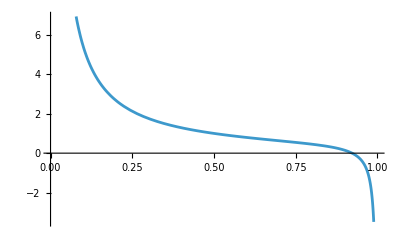

{z→0.922269}

```mathematica
data//Flatten[#,2]&
S = D[w,zi]+ (n-1)r D[w,zj]/.r-> (2Q1)/(1+Q0) /.monopop /. solFstPairs3 ;
Plot[S /.e->  0.5/.α->0/. n-> 200  /.k->1/.mp->0 /.m->0.1/. f->1.0, {z, 0, 1}]
Flatten@NSolve[S /.e->  0.5/.α->0/. n-> 200  /.k->1/.mp->0 /.m->0.1/. f->1.0 ==0,z] //Simplify
```

```mathematica
soln3
```

{z→(k (-mp (-1+n) (4+mp (-1+α)) (-1+α^2)+2 m (2+mp (-1+α)) (2 (1+n-α+n α)+mp (-1+n) (-1+α^2))-m^2 (2+mp (-1+α)) (2 (1+n-α+n α)+mp (-1+n) (-1+α^2)))+4 e^4 mp (mp (-1+n) (1+α)-2 m mp (-1+n) (1+α)+m^2 ((-1+n) (-1+α)+mp (-2+n (2+k+k α))))+e (-4 (-1+n) (1-2 m (2+mp (-1+α))+m^2 (2+mp (-1+α))+α)+k (4 (1+n-α+n α)+mp^2 (-1+n) (-1-3 α+α^2+3 α^3)+4 mp (-1+α) (-1-2 α+2 n (1+α))+m^2 (8 mp (1+α) (1+(-1+n) α)+4 (1+n-α+n α)+mp^2 (-1+α) (3+n-4 α+4 n α-3 α^2+3 n α^2))-2 m (8 (1+n-α+n α)+4 mp (1+α+2 n α+2 (-1+n) α^2)+mp^2 (-1+α) (3+n-4 α+4 n α-3 α^2+3 n α^2))))+e^3 (mp (-4 (-1+n) (3+α+2 mp α)+k mp (1+α) (3-2 α-α^2+n (1+α)^2))-2 m mp (-16 (-1+n)+4 mp (-1+n+3 α-3 n α)+k mp (1+α) (3-2 α-α^2+n (5+2 α+α^2)))+m^2 (4 (-1+n+α-n α)-4 mp (k+4 (-1+n)-k α+2 k n (1+α))+mp^2 (-8 (-1+n) α+k (7-3 α-3 α^2-α^3+n (1+α)^3))))-e^2 (8-8 n+k mp^2 (-1+α) (-1-8 α-3 α^2+n (5+8 α+3 α^2))+4 mp (-((-1+n) (1+3 α))+k (2-α-α^2+n (1+α)^2))-2 m (4 (-1+n) (-3+α)+4 mp (-((-1+n) (1+3 α))+k (3+α) (1+n-α+n α))+mp^2 (4 (-1+n+α-n α)+k (-1+3 α) (3-2 α-α^2+n (1+α)^2)))+m^2 (-4 (-1+n) (2+mp^2 (-1+α)+2 mp (1+α))+k (-4 (1+n-α+n α)+4 mp (3-2 α-α^2+n (1+α)^2)+mp^2 (1+7 α-5 α^2-3 α^3+n (1+α)^2 (-1+3 α))))))/(2 (-k (-2 m (2+mp (-1+α)) (2 n+mp (-1+n) (-1+α))+m^2 (2+mp (-1+α)) (2 n+mp (-1+n) (-1+α))+mp (4 n+mp (-1+n (-1+α)-α)) (-1+α))+2 e^4 mp (m^2 (2 mp (-1+n+k n)+(-1+n) (-1+α))+mp (-1+n) (1+α)-2 m mp (-1+n) (1+α))-e^2 (4-4 n+2 mp (k-k α+2 k n (1+α)-(-1+n) (1+3 α))+k mp^2 (-1+α) (-1-3 α+n (5+3 α))-2 m (4-4 n-2 mp (-1+n) (3+α)+4 k mp (1-α+n (3+α))+mp^2 (4 (-1+n+α-n α)+k (-1+3 α) (1+n-α+n α)))+m^2 (-4 (-1+n+k n)+4 mp (1+(-1+k) n) (1+α)+mp^2 (2 (-1+n+α-n α)+k (1+α) (3-n-3 α+3 n α))))+e (4-4 n+4 k n+2 mp (2-2 n+k (-1+4 n)) (-1+α)+mp^2 (-1+n) (-1+α) (2+k+3 k α)-2 m (4+(-4+8 k) n+k mp^2 (-1+α) (3+n-3 α+3 n α)+2 mp (-1+n+α-n α+k (3-3 α+4 n α)))+m^2 (4+4 (-1+k) n+k mp^2 (-1+α) (1+n-3 α+3 n α)+2 mp (-1+n+α-n α+k (2-2 α+4 n α))))+e^3 mp (-2 (-1+n) (3+α+2 mp α)+k mp (1+α) (1+n-α+n α)-2 m (8-8 n+mp (k-k α^2-2 (-1+n) (-1+3 α)+k n (5+2 α+α^2)))+m^2 (-2 (2+mp) (-1+n) (1+α)+k (-2-8 n+2 α+mp (3-2 α-α^2+n (1+α)^2))))))}